### A ReadMe file SSAH ReadMe.nb (click it ) is available for help in running this program. © K. A. Holsapple, 2018, 2019, 2020, 2021. New users wishing to change or understand the code are encouraged to get a Mathematica tutorial book , or there are many online tutorials. A ‘Cookbook’ is available here. This version includes the ability for the population to change with time from fragmentation and depletion. After code changes, it is prudent to save, quit and restart SSAH. There may be a few gremlins hiding in the dark corners. To begin, put cursor anywhere in the cell below and hit “Enter” (not “return”) ..

```mathematica
mversion="P_2.4"; (* variable population allowed again*)
dir=NotebookDirectory[];
(*SetOptions[$FrontEnd,InitializationCellWarning->False];*)
nb=EvaluationNotebook[]; (* G: gives the notebook in which this function is being evaluated. *)
$PlotTheme={"Scientific","Grid","LargeLabels"};
(*SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];*)
localtime0=LocalTime[];
If[!ValueQ[firsttime],firsttime=True,firsttime=False]; (* load it the first time *)

CloseAllInputCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"]; (* G: Module defines local variables *)
SetOptions[#,CellOpen->False]&/@cells;opentest=False];

OpenAllInputCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->True]&/@cells;opentest=True];

SetOptions[$FrontEndSession,InitializationCellEvaluation->True(*{InitializationCellEvaluation->True,InitializationCellWarning->False}*)];

image=-Graphics-;
depleteplot=-Graphics-;
(*(*FrontEndTokenExecute["DeleteGeneratedCells"] ;*)
discard=ChoiceDialog["Do You Want To Discard Previous Output?",{Yes->True,No->False},WindowMargins->{{Automatic,Automatic},{Automatic,Automatic}}];
If[discard,
FrontEndTokenExecute["DeleteGeneratedCells"]];
*)

If[firsttime,(*  first time *)Speak["Welcome! This is Ess, Ess, A, H. A program to make simulations of billions of years of the history of asteroids in the main belt. Make a choice to start!"];

opentest=True; (* flag for close source code *)
pic1=Import[filename=FileNameJoin[{dir,"Info Files","Appendix O.  GeneralOutline.pdf"}],"PageGraphics"];
pic2=Import[filename=FileNameJoin[{dir,"Info Files","Appendix F.pdf"}],"PageGraphics"];
pic3=Import[filename=FileNameJoin[{dir,"Info Files","Appendix L.pdf"}],"PageGraphics"];
piccrater=Import[filename=FileNameJoin[{dir,"Data","lunarcrater.png"}],"PNG"]
];

Overlay[
{image,

Column[{
PopupWindow[Button[Style["SSAH General Outline",Blue]],pic1,WindowSize->{700,800},WindowElements->{"VerticalScrollBar","HorizontalScrollBar"}],PopupWindow[Button[Style["SSAH Function List",Blue]],pic2,WindowSize->{700,800},WindowElements->{"VerticalScrollBar","HorizontalScrollBar"}],
PopupWindow[Button[Style["SSAH Calculation Logic",Blue]],pic3,WindowSize->{700,800},WindowElements->{"VerticalScrollBar","HorizontalScrollBar"}],
Button[Style["Hide/Show Source Code",12],If[opentest==True,CloseAllInputCells[],OpenAllInputCells[]]
],
Button[Style["Open Sample Input File",16],NotebookFind[EvaluationNotebook[], "topend", All, CellTags];
SelectionEvaluate[EvaluationNotebook[]]]}]

}
,All,2,Alignment->{-.9,-.3}](*G: Create the image and overlay text and sets link. Calls the topend cell*)
```

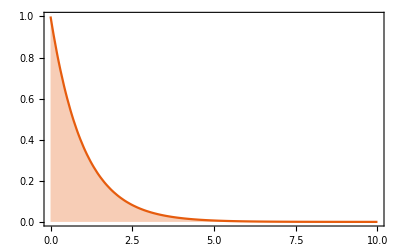
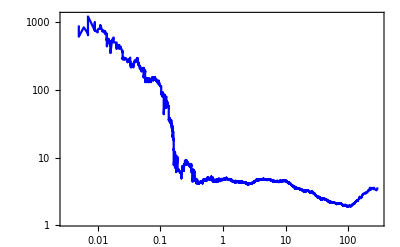
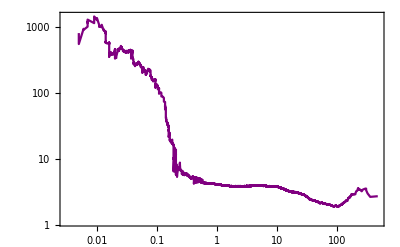
```mathematica
(* all the functions in alphabetical order *)

(*--------Eliminate entire pulverized targets and its impactors -----  *)
addtopopchange[binnum_,binnumt_]:= (* pulverized target or impactor.  for impactor scale by the target numbers *)
(popchange[[binnum]]=popchange[[binnum]]-1*diffdistr[[binnumt]]/ntopick[[binnumt]];)
(*------------------End of addtopopchange function------------------------*)

(* -----a function to get pd number and bin from its diameter ----*)
astnum[dia_]:=({Ceiling[nfun[dia]],FirstPosition[cumdistr[[All,1]],x_/;x<dia][[1]]-1})
(*if it is below the bin descriptions, i set the bin number to numcum, 
    which is one more than the number of bins *)
(*--------------------end of astnum function-------------------------------*)

(*-------Load the properties for a given asteroid type-----------------------*)
asttypestuff[name_]:=(If[name=="S-Type",
mu=0.55;
dens=2.5 10^12;
(*dens=3. 10^12;*)
Y0=1.5 10^10; (*our granite size effects test had this value*)
	(*Y0=3 10^10;*)  (*kg/km/sec^2;*)(*dynes/cm^2 *100 -> kg/(km sec^2)->kPa *)
	(*Y0=0.7 10^10;*)(* best for gaspra*)
 (*kg/km/sec^2;*)(*dynes/cm^2 *100 -> kg/(km sec^2) *)
	(*Y0=1.5 10^11;*) (*for eros*)
d0strength=1 10^-4;(*km*)
nsize=4; (* strength decreases with size as 1/nsize *)
(*nsizespall=2;*)
nsizespall=2;  (*our granite size effects test had this value*)
k2s=0.3; (* ejecta scaling for vstar*)
k2g=0.3;
k1=0.05;  (* for cratering, quite arbitrary *)
       k2=1.; (* the cratering constant *)
       kr=1.1;
qconst1=10^-3;
qconst2=1.;
ke=0.06;  (* not used now *)
(* spall stuff *)
	kv=0.08;
	kt=0.0;
	mfac=2.;
	KS=12.5; (*Polanskey value *)
,
(* otherwise -C-Type *)
mu=0.41;
dens=1.5 10^12;
Y0=1.5 10^8;
d0strength=10^-4;
nsize=4; (* almost no size dependence *)
 nsizespall=2;
k2g=0.3; (* ejecta scaling for vstar*)
k2s=0.3;
k1=0.15;  (* for cratering, quite arbitrary *)
       k2=1.;
       kr=1.2;
qconst1=2 10^-3;  (* direct from Qstar paper *)
qconst2=0.5;
ke=0.02(* not used now *);]
)

    (*--------------end of asttypestuff function-------------------------------------------*)

(*--------------barscale function-------------------------------------------*)
barscalef[]:= (* assumes units of dimensions are km*)(bar=Graphics[{Green,Thickness[.005],Line[{{1,1.2},{1,.8},{1,1},{2,1},{2,1.2},{2,1},{11,1},{11,1.2},{11,0.8}}]}];
label1=Graphics[{Green,Text[Style["1 km ",12],{1.5,1.2}]}];
label2=Graphics[{Green,Text[Style["10 km ",12],{10,0.8}]}];
Show[bar,label1,label2])(*--------------end of barscale function-------------------------------------------*)



(* -----------bumpfun-----------------------------------------------------*)
bumpfun[n1_,n2_,n3_,fac_]:=(multlist=Table[If[n1<n<n2,1+fac Sin[Pi(n-n1)/(n2-n1)],1],{n,n3}])
(* ---------end of --bumpfun-----------------------------------------------------*)

(*------the crater sizes from crater scaling--------------------------
cratr size not related to escaping mass -----*)

calccrater[di_,dtarg_,vel_,type_] := 
  (* type=3 when getting largest expected craters without disruption,
   type=2 for all real craters, 
type=1 when getting largest epected crater at various probabilities *)
    (* the velocity is the normal component *)
    (
	kv=0.08;
	kt=0.05;
	mfac=2.0;
        KS=12.5;
(* reset parametersfor each asteroid *)
Which[newname=="Eros",
	Y0=1.5 10^11;
	dens=2.67 10^12,	
newname=="Gaspra",
	Y0=0.7 10^10;
	dens=2.7 10^12,
newname=="Ida",
	Y0=0.7 10^10;
	dens=2.7 10^12,
newname=="Ceres",
	Y0=.5 10^10;
	dens=2.16 10^12;
	mu=0.6];

	rt=dtarg/2;
	ai=di/2;
      grav=2 Pi/3  6.67 10^-20 dens dtarg;   (*mks units -> km, kg,s*)
      mass=Pi/6 densi di^3;

    (* strength regime uses size-depend strength ~ 1/nsize, see file CraterScaling.nb *)
    piv=pivf[di,nsize];
    volc=piv mass/dens;
    massc=volc dens;
    dc=2 kr volc^(1/3);(*bowl, redone for spall below*)
    dcrim=1.3 dc;
If[type==1,AppendTo[dcrimdias,{impacttime,dtarg,dcrim,di}]; ];
    (*If[type==3,AppendTo[dcrimdias2,{dtarg,dcrim/dtarg}] ];*)
(* limits *)

 dspstar=d0strength(kv^2 Y0/(2 mfac grav dens kt  d0strength) )^(nsizespall/(nsizespall+1));
 dccomlim=(81/(2*Pi))^(1/(1 + 1/nsize))*(Y0/((1/d0strength)^nsize^(-1)*(dtarg*Grav*dens^2)))^(1/(1 + 1/nsize));
dcs=KS ai (ai/d0strength)^(mu/(2 nsizespall -mu))(Y0/(dens vel^2))^(-mu/2);  

If[dcs<dspstar,
	(* spall crater diameter *)
  AppendTo[spalldias,{impacttime,dtarg,dcs,di}];
  dforlarge=dcs, 

(*maybe complex? *)
If[dcrim>dccomlim,
   dcomplexrim=1.33 dc^1.086 dccomlim^-.086; 
   AppendTo[complexdias,{impacttime,dtarg,dcomplexrim,di}];
  dforlarge=dcomplexrim, 
(* not spall nor complex *)
 
If[type!=1,AppendTo[dcrimdias,{impacttime,dtarg,dcrim,di}];
  dforlarge=dcrimdias ]]];
 
  )    
(*----------------end of calccrater-------------------------------------------*)



(*------------------calcnasteroids[]------get the test asteroids---------------------*)
calcnasteroids[]:=(If[Negative[testratio],nasteroids=-testratio;Do[bin=RandomInteger[{binfirst,binlast}];
++ntopick[[bin]],{i,nasteroids}],
 (* otherwise *)   Do[ntopick[[ibin]]=Ceiling[If[ibin<=binlast1,testratio diffdistr0[[ibin,2]],testratio diffdistr0[[binlast1,2]]](*(binfirst/ibin)^3*)]; 
(* last factor designed to pick less small ones to better compare to the data, 
    it is quite arbitrary  maybe it deserves its own input box *)
(* if exact, it picks testratio times all in enclosing bin for that diamter*)
,{ibin,binfirst,binlast}];
nasteroids=Total[ntopick];
];
nasteroids)
(*-------------end of calcnasteroids function----------------------------------------*)


(*------calculate the spin increment, check for wobble/tumbling, new inertia set for reduced size*)      
  (* and if, a cdevent-----------------------------------*)
(*I did redo this, and just let all targets be wobblers and track wobbling down to zero. then plot only those wobbling above some threshhold value.  i do not need the tumblers array.  *)


calcomega[iflag_]:= (* sti.00ll has old d *)
(* iflag->{0,1,2}  relax only, also calc impact, close last time (same as 0 )*)
((* first calculate  new lateral components, then the relaxation of tumblers, and add the new increment from the impact..  trelax is set for this impact and target*)

(* old ones *)
{omegx,omegy,omegz}=omeg;
omegnet=Sign[omegz] Norm[omeg];
wobble=ArcTan[Sqrt[(omegx^2+omegy^2)]/Abs[omegz]]; (* last wobble, in radians, *)
(* let 1 degree be zero wobble, and adjust relax time to 1˚ *)

If[Im[wobble]>0,Print["here 1, wobble not real "];Abort[]];
If[wobble<1Degree,wobble=0];
(* get new random lateral compoments with same lateral magnitude *)
angle=RandomReal[{0,2Pi}];
oomeg=Sqrt[omegx^2+omegy^2];
omegx=oomeg Cos[angle];  (* Couldn't understand why: Gaurav *)
omegy=oomeg Sin[angle];

(* get decay since last hit.. it may have decayed to the PA spin.  
If so, add a plot point at PA values.  if it was zero, it still is zero *)
(*Print["in calco, wobble,tsince,trelax= ",{wobble,impacttime-tlasthit,trelax}];*)
(*Print[" old values {impactor,iast,wobble,trelax,tlasthit,trelax+tlasthit,impacttime} ",{ii,iast,wobble,trelax,tlasthit,trelax+tlasthit,impacttime}];*)

If[wobble>1 Degree,
If[(trelax+tlasthit<impacttime),(* relaxing to <1˚ (zero) since last hit, add previous time point *)
(*Print[" relaxing to zero.. "];Print[" {impactor,iast,wobble,trelax,tlasthit,,trelax+tlasthit,impacttime} ",{ii,iast,wobble,trelax,tlasthit,trelax+tlasthit,impacttime}];
*)omeg={0,0,Sign[omegz](Sqrt[jinertia[[3]]^2omegz^2+jinertia[[1]]^2omegx^2+jinertia[[2]]^2omegy^2]/jinertia[[3]])}; (* Burns and Safranov, constant angular momentum magnitude *)
omegnet=Sign[omeg[[3]]] Norm[omeg];
omegvals[[iast]]=omeg;
wobble=0;
 If[plothis>0&&d>0,
 AppendTo[histplotpts[[plothis]],{trelax+tlasthit,d,omegnet,0}];
   AppendTo[histplotpts[[plothis]],{impacttime,d,omegnet,0}]],

(* or did not relax to zero, so get relaxation changes *)
(*Print["calling wobblecalcf,omeg, wobble,trelax,impacttime-tlasthit= ",{omeg,wobble,trelax,impacttime-tlasthit}];*)   
 wobblecalcf[];
If[plothis>0&&d>0,
AppendTo[histplotpts[[plothis]],{impacttime,d,omegnet,wobble}]]],
(* wobble<1˚ *)
If[plothis>0&&d>0,
AppendTo[histplotpts[[plothis]],{impacttime,d,omegnet,0}]]
]; (* new relaxed omega, wobble, omegnet *)

(* now the changes from the new impact *)

If[iflag==1,
(* not the last point at the end time, add impact increments *) (* but what should i do in the last time?*)

zeta= zetaf[phival,d,asttype];  (* uses the old d if it depends on d *)
(* now add impact increment, account for a non-spherical target *)
delamomentum=r mass vel Sin[phival]zeta{-Sin[thetaval]Cos[Thetaval]Cos[Phival]-Cos[thetaval]Sin[Thetaval],-Sin[thetaval]Sin[Thetaval]Cos[Phival]+Cos[thetaval]Cos[Thetaval],
Sin[thetaval]Sin[Phival]};

delomeg=delamomentum/jinertia;
(* uses old inertia of ellipsoidal in principal axes*)
(* should i use previous d inertia or decreased one?*)
(* i now use new inertia *)
omeg=omeg+delomeg;  
(* that is the increment from the imapct *)

delomegdrain=If[qratio<.5,drainfac omegdrainf[],{0,0,0}]; (* 3 components,  parallel to omeg negative in function *)
(* now the splash *)
xx=0.5/Log[pulvlim];
	dnew=d(.5-xx Log[qratio])^(1/3);;
delomegsplash=If[qratio>.5,-omeg splashfac(1-(dnew/d)^3),{0,0,0}]; (* same here *)(* Cellino et al. proportional to deltaM/M *)
delomegds=delomegdrain+delomegsplash;
delomeg=delomeg+delomegds;
        
omeg=omeg+delomeg;

omegnet=Sign[omeg[[3]]] Norm[omeg];
{omegx,omegy,omegz}=omeg;
omegzz=Sign[omegz] Max[Abs[omegz],10^-9];
wobble=ArcTan[Sqrt[omegx^2+omegy^2]/Abs[omegzz]];
If[Im[wobble]>0,Print["here 2, wobble not real "];Abort[]];
If[wobble<1 Degree,wobble=0];

(* spin now determined *)
lastimptime[[iast]]=impacttime ]
 
(*end of omega update end of last time*)

)
(*---------------end of calcomeg function---------------------------------------*)


(* now this is random *)
 combinedspinlimf[d_,dcenter_,gravlimhere_,spinflg_]:=(
(*Print["in combinedspinlim ",{d,dcenter,spinupratio,spinflg}];*)
omeglimstrength=If[d>0,Min[(2Sqrt[2.25 10^7/2.5](10^5d/2)^-(5/4)),Y0],Y0];
(*omeglimstrength= 10^4;*) (* a non-factor *)
currentspinlim=If[d>2dcenter,gravlimhere,If[d<dcenter/3.5,omeglimstrength,If[spinflg,omeglimstrength,gravlimhere]]])

(*currentspinlim=If[d>dforgravlimnow,gravlimit,omeglimstrength]*)(*koverrho=(gravlimit^2)/4 (  diaforgravlim 10^5/2)^(5/2)*)
(*Max[omeglimstrength strengthfac+(1-strengthfac) gravlimit,gravlimit]*)
(* ------------end of combinedspinlimf ------------------------------------------*)


(* -----------make the crater scaling plot if all targets are the same size--------- *)
craterscalingplotf[]:=(
asttypestuff["C-Type"];
colors=RandomColor[7];

plotc=Show[Table[LogLogPlot[pivpi2f[pi2,3.9,10^ii,4],{pi2,10^-10,10^-2},Frame->True,FrameLabel->{"Pi2=g a/U^2","Piv=rho V/mass-impactor"},LabelStyle->24, PlotStyle->colors[[ii]]],{ii,-2,3}],Graphics[Text[Framed[Style["Curves from botom to top are for\r target diameters of {0.01, 0.1, 1, 10, 100, 1000} km ",12]],Scaled[{.3,.5}]]],ImageSize->Full,PlotRange->All];

asttypestuff["S-Type"];
plots=Show[Table[LogLogPlot[pivpi2f[pi2,3.9,10^ii,4],{pi2,10^-10,10^-2},Frame->True,FrameLabel->{"Pi2=g a/U^2","Piv=rho V/mass-impactor"},LabelStyle->24, PlotStyle->{Dashed,colors[[ii]]}],{ii,-2,3}],ImageSize->Full,PlotRange->All];

craterscaling=Show[plotc,plots,Graphics[Text[Framed[Style["The crater volume scaled to the impactor mass m\r as a function of the impactor diameter. \rDashed->S-Type, Solid->C-Type.  \rThe values on the left are the strength regime, \rthe deceasing on the right is a consequence of increasing gravity forces",12]],Scaled[{.5,.2}],Background->LightGray]]])


(* ----------------------------end of craterscalingplotf---------------------------*)

(*(* bin data in multiples of ratio*)
databinned[list_,ratio_]=
(biggy=1.00001list[[1]];
nnum=-(Log[Min[list]]-Log[biggy])/Log[ratio];
cumnums=Accumulate[Table[Length[Select[list,biggy/(ratio^(i-1))>#>biggy/(ratio^i) &]],{i,nnum}]];
binpts=Table[{Mean[Select[test,biggy/(ratio^(i-1))>#>biggy/ratio^i &]],cumnums[[i]]},{i,1,nnum}])
*)




(*----------------------find binnumber for ast number n--------*) (*--------------------the bin number n has the n+1 and nth boundaries--------*)
dbinf[n_]:=(FirstPosition[cumdistr[[All,2]],_?(#>n&)]-1);
(*----------------End of dbin function--------------------------------------------*)


(*---------------Several depletion models -----------------------------------*)
depletion[x_]:=(Piecewise[{{0.003 x^(-1),3<x≤20},
{0.0014 x^(-2.2/7),0.25<x<=3},{0.00114 x^-0.5-8.75 10^-5,0.02<x<=0.25},
{0.05756 Sqrt[x]-0.000141,0.004<x<=0.02},{9.7768 10^-5 x^(-2/3)-0.00038,0.0001<x<=0.004}}])

depletion3[x_]:=(Piecewise[{{0.00114 x^-0.5-8.75 10^-5,0.02<x≤20},{0.05756 Sqrt[x]-0.000141,
0.004<x<=0.02},{9.7768 10^-5 x^(-2/3)-0.00038,0.0001<x<=0.004}}];)

depletionbottke[x_]:=(Piecewise[{{.0003,0.001<x≤1},{.0003-2.44 10^-5(x-1),1<x≤10},
{.00008-8 10^-6(x-10),10<x≤20},{0,20<x≤1000}}])

depletionbottke2[x_]:=(Piecewise[{{.0003,0.001<x≤1},{.0003-2.44 10^-5(x-1),1<x≤10},
{0,10<x≤1000}}])
(*----------------End of depletion function--------------------------------------------*)


(*---------------- dfac function--not now used-----------------------------------------*)
dfacf[]:=(dfac= Max[1,Log[10,10d^1.5]]; (* first guess *)
xvals=Log[{.001,5.,8.,30.,50.,100.,1000}];(* pts for tweaking *)
dfacvals=Table[dfac/.d->E^xvals[[i]],{i,7}];
yvals=Log[{1.,1.,1.5,1.45,.5,1.,1.}]; (* additional corrrection *)
yvals=Log[dfacvals]+ yvals; (* add in log space *)
funcpts=Transpose[{xvals,yvals}];
dfac=Interpolation[E^funcpts,InterpolationOrder->1];
)
(*----------------End of dfacfunction--------------------------------------------*)

(*--------Find a power law fit to the first num points in a distribution formatted as a list--------------------------------------------------*)
distfitf[dist_,num_]:=
(fit=FindFit[Part[dist,1;;num],{cdd x^-alp},{{alp,2.2},{cdd,2 10^6}},x];
alphax=alp/.fit[[1]]; (* alpha is a positive number *)
cdx=cdd/.fit[[2]])
(*----------------End of distfitf function====-------------------------------*)

 (*------------------ eroded to zero -------------------------------------*)
erodedtozerof[]:=(  (* two cases??, replaced or not *)
If[bornagain,(*need to reset stuff*) 
d=d0;
dlist[[iast]]=d0;

(* now reset spin *)
omegvals[[iast]]=resetomegf[d]; (* 3 components for each target, not wobbling *)

omeg=omegvals[[iast]]; 
omegnet=Sign[omeg[[3]]] Norm[omeg];
omegzz=Sign[omegz] Max[Abs[omeg[[3]]],10^-9];
wobble=ArcTan[Sqrt[(omeg[[1]]^2+omeg[[2]]^2)]/Abs[omegzz]];
(* take it off binary list *)
(*Print["in eroded to zero, take off binary list"];*)
binaries=Complement[binaries,Select[binaries,#[[1]]==iast &]],
(* note that now these are candidates for binaries, maybe not actual *)
(* otherwise... will kick out for small diameter *)
d=0.;
dlist[[iast]]=0.;
]
 )
 (*------------------eroded to near zero -------------------------------------*)
(* -----the function to get the fragment sizes and numbers and bins.----------*)
fragments[qratio_]:=
(dlast=d;(* it is changed below *)
(* now this does not get the largest, only the fragments, so it is only used when allowing variable population. *)

binnumtnew=astnum[d][[2]];
   diaf2=d*(0.1 qratio^.9)^(1/3);
diaf3=(0.4)^(1/3) diaf2;
firstthree={d,diaf2,diaf3};
first3bins=Table[astnum[firstthree[[i]]][[2]],{i,3}];
bin3=first3bins[[3]];
(* target diminished, reduce cum dist from bin+1 of target to end*)
firstset=Table[0,{i,numcum-1}];
subtract=firstset; (*another zero set  *)
subtract[[binnumt]]=1; (*dump target, now included in largest frag*)
subtract[[binnumi]]=1; (* dump impactor*)

ntodo=3;
If[first3bins[[3]]>numcum-1,ntodo=2];
If[first3bins[[2]]>numcum-1,ntodo=1];
If[first3bins[[1]]>numcum-1,ntodo=0;];

Do[firstset[[first3bins[[i]]]]=1,{i,ntodo}];  (*will need to accumulate*)

(*now the rest of the frag addditions *)
(*Print["is there a problem here?",diaf3, "qratio= ",qratio];*)

If[ntodo==3,
(boundaries=Table[cumdistr[[i,1]],{i,bin3,numcum}];
boundaries[[1]]=diaf3;
(* these are the frag numbers in each bin*)
alp2=(5.4058586727114*^15-7.22418332833735*^15 qratio^(59/510)+3.612091664168675*^15 qratio^(9/10))/
 (5.4058586727114*^15-4.784668666890982*^15 qratio^(59/510)+2.392334333445491*^15 qratio^(9/10));
(*Print["alp2= ",alp2];*)
rm=.08;
kk=(3rm^((alp2-5/4)))^(1/3);
(*this new alp2 is based on exactly 100% mass in the fragments all the way to zero mass.  see the file fragmasstry8.nb*)
fragnumbers=PadLeft[Table[nnfrags[boundaries[[i+1]]]-nnfrags[boundaries[[i]]],{i,1,numcum-bin3}],numcum-1];)
,
fragnumbers=ConstantArray[0,numcum-1],Print["ntodo= ",ntodo]];
(* these are the numbers from the frag distribution going into the bins of the population distribution *)
(*Print["d= ",d,"\r boundaries ",boundaries,"\r fragments for this hit ",fragnumbers];*)
(*Print["old popchange= ",popchange];*)
popchange[[binnumt0]]=popchange[[binnumt0]]+(fragnumbers+firstset-subtract); 
(* this accumulates over the asteroid hits in each time step *)
fragdistr0=Transpose[{diffdistr0[[All,1]],Accumulate[fragnumbers]}];
newmass=Total[firstthree^3]+Total[massindist[fragdistr0]];
mlost=(dlast^3-newmass)/dlast^3;

)
(*-----------------End of Fragments function-----------------------------------*)
(*---given distr, find the diameter for a given numer by interolation assuming a power-law --*)

getdiaf[num_]:=(
pos1=FirstPosition[cumdistr[[All,2]],_?(#>num&)];
pair2=cumdistr[[pos1]][[1]];
pair1=cumdistr[[pos1-1]][[1]];
alpnow=-Log[pair1[[2]]/pair2[[2]]]/Log[pair1[[1]]/pair2[[1]]];
di=pair1[[1]](num/pair1[[2]])^(-1/alpnow))
(*-----------------End of getdiaf function-----------------------------------*)

Attributes[getdiaf]={Listable};


(*-------Histograms of the spin nomalized to their average------not used?------------*)
histogramofnormalizedf[list_,num_]:=(meanarray=Table[meaninrangef[list,list[[i,1]]],{i,Length[list]}];
normalizedpts=Table[list[[i,2]]/meanarray[[i]],{i,Length[list]}];
Histogram[normalizedpts,num])
(*-------------end of histogramofnormalizedf function--------------------------*)

(*-------histograms of the spin around a diameter ----often used--------------*)
histogramf[list_,d1_,d2_,minval_,type_,nn_,name_]:=
( (* the spin  comes in and goes out with same units *)
group=Select[list,(d1<=#[[1]]<=d2)&&#[[2]]>minval&][[All,2]];
meangroup=Mean[group];
     mediangroup=Median[group];
maxgroup=Max[group];
mingroup=Min[group];
num=Length[group];
(*Print[{group,num,d1,d2}];*)
histo=If[type=="Log",Histogram[group,{"Log",nn},ImageSize->500,Frame->True,FrameLabel->{"Spin, cycles/day","Number"},LabelStyle->24,PlotRange->{{.01,12},Automatic}],Histogram[group,nn,type,ImageSize->500,Frame->True,FrameLabel->{"Spin, cycles/day","Number"},LabelStyle->24,PlotRange->{{0,12},Automatic}]];
maxheight=Max[HistogramList[group,nn,type][[2]]];
line=ListPlot[{{meangroup,0},{meangroup,1.2maxheight}},Joined->True,PlotStyle->{Thick,Black}];
Show[histo,line,Graphics[Text[Framed[StringForm["This is the  distribution for the `5` \n of `6` asteroids from  `1`  to `2` km diameter.  \nThe mean is `3`  , The median is `4`",d1,d2,N[meangroup,3],N[mediangroup],name,num,type]],Scaled[{.95,.9}],{1,1},Background->White,BaseStyle->{16,FontFamily->"Times"}]],ImageSize->Full,
Frame->True,FrameTicksStyle->20,
PlotRange->All])

(*-------------End of histogramf function------------------------------------*)
 

(*-------------End of histogramf function------------------------------------*)
(* -----------------set initial values for spins  really irrevelant? yes, for large ones..----
but not too much wobble?---*)

initialspins[]:=(spinrange={-6,-5};(* these are .013 to 0.14 cycles/day *)
(*these have little affect for small ones, but definite effect for those ~100km *)
(*Table[
{(RandomChoice[{-.01,0.01}]10^RandomReal[spinrange]),(RandomChoice[{-0.01,0.01}]10^RandomReal[spinrange]),(RandomChoice[{-1.,1.}]10^RandomReal[spinrange])},{nasteroids}]*)(*Changed by Gaurav*)
Table[
{0,0,(RandomChoice[{-1.,1.}]10^RandomReal[spinrange])},{nasteroids}]
)
(* -----------------end of initial values for spins -------*)

(*-----------escaping mass---------------------------------------------------*)
   massescf[]:= (* this ignores the effect of spin on escaping mass *)
(Un=vel Cos[phival];
(* the equation (35) of "collision spins" works for either strength or gravity regimes and is independent of gravity and/or strength, but needs vstar limit *)
massc=pivf[diameter,nsize] mass;
mstar=0.6 massc;
massesc=If[vesc>vstar,mstar  (vesc/vstar)^(-3mu),mstar])
  (*--------------end of massescf----------------------------------------------*)

(*-----------calculate the mass content of a population distribution----used only when calculating mass blance...-------*)
massindist[dist_]:=
(* strip first zeroes *)
(If[Max[dist[[All,2]]]>0,
(posfirst=Position[dist[[All,2]],_?Positive][[1]][[1]];
distnow=Drop[dist,posfirst-1];
ndist=Length[distnow];
slopes=-Table[Log[distnow[[i,2]]/distnow[[i+1,2]]]/Log[distnow[[i,1]]/distnow[[i+1,1]]],{i,1,ndist-1}];
d2vals=Drop[distnow[[All,1]],-1];
d1vals=Drop[distnow[[All,1]],1];
n2vals=Drop[distnow[[All,2]],-1];
massvals=(slopes/(3-slopes)) n2vals(d2vals^3)(1-(d1vals/d2vals)^(3-slopes)))
,massvals=ConstantArray[0,Length[dist]]
];)
(*-----------------End of massindist function---------------------------------*)

(*-------(* the largest expected at various probabilities *)------for crater count plots--------------*)
maxexpectedcraterf[facvals_]:=(
(* since the populations might vary in time, i use here the average of the original and the present ones *)
(*distfitf[cumdistr,20]; (* sets alpha0, cd of the new distribution *)
alpha1=alphax;
cd1=cdx;
cd=(cd0+cd1)/2;
alpha=(alpha0+alpha1)/2;*)

dl=fac(probi cd0 (dt/2)^2 tmax)^(1/alpha0);
(*dl=fac(probi cd (dt/2)^2 tmax)^(1/alpha);*) (* largest expected impactors *)
(* but the population changes in time..*)
massvals=Pi/6 densi dlvals^3;
vel=velave;
phival=45Degree;
velbar=vel Cos[phival] ;
calccrater[dl,dt,velbar,3];
(*Print["here2, dcrim= ",dcrim];*)
dcrimvals2=dcrim/.fac->facvals;
plotbowllimits=LogLogPlot[((dcrimvals2/dt)),{dt,10,300},PlotStyle->{Pink}];

(* the call to calccrater returns dccomlim, but not dcomplexrim, so just calculate it *)
dcomprimvals=(1.33 dc^1.086 dccomlim^-.086)/.fac->facvals; 
plotcomplexlimits=LogLogPlot[dcomprimvals/dt,{dt,250,1500},PlotStyle->{Pink,Dashed}];)
(*-----------------End of maxexpectedcraterf function-------------------------*)

(* huh?... *)
maxcraterinbinsf[nwanted_]:=
(ratio=Table[0,20];
plotpts13=ratio;
plots=Table[0,{i,Length[nwanted]}];

(* since the populations vary in time, i use here the average of the original and the present ones *)
(*distfitf[cumdistr,20]; (* sets alpha, cd of the new distribution *)
alpha1=alphax;*)
(*cd1=cdx;
cd=(cd0+cd1)/2;
alpha=(alpha0+alpha1)/2;*)
cd=cd0;
alpha=alpha0;
Do[
d1vals=Table[bindias[[i]],{i,20}];
dlargestvals=(probi cd (d1vals/2)^2 tmax)^(1/alpha);
(* but the population changes in time..but not much at top end! *)
numbers=Table[diffdistr0[[i,2]],{i,20}];
 p1vals=Table[Min[.5,nwanted[[j]]/numbers[[i]]],{i,20}];
betavals=(-Log[1-p1vals])^-(1/alpha0);
Do[
calccrater[dlargestvals[[i]] betavals[[i]],bindias[[i]],vel Cos[45Degree],3] ;
ratio[[i]]=dforlarge/(bindias[[i]]);

plotpts13[[i]]=If[p1vals[[i+1]]<.5,{bindias[[i]],ratio[[i]]},{bindias[[i]],0}]
,{i,19}];

plots[[j]]=ListLogLogPlot[plotpts13,PlotStyle->{Dashed,Red},Joined->True,PlotMarkers->{Automatic,7},
PlotRange->{.1,2}];
,{j,Length[nwanted]}];
plotforbiggies=Show[plots];)(*-----end of maxcraterinbinsf function -------------------------------------*)


(*-----------find mean in a box around diameter d----------------------------  *)
meaninrangef[list_,d_]:=(Mean[Select[list,1/1.1 d<#[[1]]<1.1 d&][[All,2]]])
(*--------------------end of meaninrangef function----------------------------*)

(* ------a function to get the diameter for any number in the distribution -----*)
nfun[dd_]:=(Interpolation[cumdistr][dd])(* creates a interpolation function to  to get the number for any diameter dastnum[] uses it*)

(*-------------------find n from diameter------------------------------------*)
nnfrags[dia_]:=
(*(1/(1/(3(dia/diaf3)^-(15/4))+1/(kk(dia/diaf3)^(-3 alp2)))*)
(Round[(Min[3(dia/diaf3)^-(15/4),kk(dia/diaf3)^(-3 alp2)] )])
(*-----------------End of nnfrags function-----------------------------------*)

(*-----------------multiptf function- piecewise linearfunction in log space-now not used...------*)
multiptf[x_,list_]:=
(nl=Length[list];
seg=Table[{},{nl-1}];
xvals=list[[All,1]];
yvals=list[[All,2]];
(*Print[{xvals,yvals}];*)
Do[{x1,x2,y1,y2}={xvals[[ii]],xvals[[ii+1]],yvals[[ii]],yvals[[ii+1]]};
exp=(Log[y2/y1])/Log[x2/x1];
seg[[ii]]=y1 (x/x1)^exp;
,{ii,nl-1}];
function=Piecewise[Table[{seg[[ii]],xvals[[ii]]<x<xvals[[ii+1]]},{ii,nl-1}]])
(*-----------------End of multiptf function-----------------------------------*)

(*------------The drain effect on spin increment------------------------------*)
omegdrainf[]:= (* I assume the following are set before this call : dens,densi,omegs,diameter, mass,piv,r,mu,omeg,  ,k2s,k2g
this is the D&B formulation for a single hit*)
(Y=Y0(d0strength/(2r))^(1/nsize);

rc=vstar/(Sqrt[2]omegs);
massc=piv mass;
masseject=0.6 massc;
ra=rc (masseject/mass)^(1/(3 mu));
delomegdrain=-5/12 3 mu omeg(mass/Mkg)(r/ra)^-(3mu);
drain=If[r>rc,delomegdrain,0];
(*Print[{vstar,r,rc,ra,drain}];*)
drain
)
(*------------end of omegdrainf------------------------------------------------*)


(*Primary Function for calculating Yorp*)

Yorp[]:=(

While[impacttime>time0+10, 
SetDirectory["/Users/kumargaurav/Documents/OrbFit/tests/gaurav"];
RunProcess["make"];
yark=Import["/Users/kumargaurav/Documents/OrbFit/tests/gaurav/yarkovsky.in","Table"];
If[FailureQ[yark],Print["Failed in importing the data from yarkovsky.in"]; Abort[]];
yark[[1,7]]=2* Pi/(omeg[[3]]*3600);
yark[[1,6]]=obliq;
resultExport=Export["/Users/kumargaurav/Documents/OrbFit/tests/gaurav/yarkovsky.in",yark,"Table","FieldSeparators"->"    "];
If[FailureQ[resultExport],Print["Failed in exporting the yarkovsky.in"]; Abort[]];
exitcode=RunProcess["./orbit9.x","ExitCode"];
If[FailureQ[exitcode],Print["Failed in running orbit9"]; Abort[]];
omegOrb=Import["/Users/kumargaurav/Documents/OrbFit/tests/gaurav/clo0.yorp","Table"];
If[FailureQ[omegOrb],Print["Failed in importing the data from orbit9"]; Abort[]];
omeg[[3]]=2*Pi/(omegOrb[[Min[Round[(impacttime-time0)/100],1000],2]]*3600);
obliq= omegOrb[[Min[Round[(impacttime-time0)/100],1000],3]]; 
SetDirectory["/Users/kumargaurav/Documents/Asteroids"];
If[omeg[[3]]>0.90*omegaLimit,Print["Too fast spinning causing landslides"]; Landslides[];]; 
(*Print[omeg[[3]]];*)
time0=time0+10^5;
If[impacttime<time0,time0=impacttime];
AppendTo[myomega,{time0,omeg[[3]]}];]
Print["Omega after the yorp effect", omeg[[3]]];
)





(* Primary Function for calculating landslides *)

Landslides[]:= (

d=d/(1+parameters[[Position[parameters,"uni_h"][[1,1]]]][[2]]*epsilon);
parameters[[Position[parameters,"omega"][[1,1]]]][[2]]=omeg[[3]]/(G*4/3* Pi*dens/10^9)^0.5;
parameters[[Position[parameters,"slides"][[1,1]]]][[2]]=IntegerPart[slides];
parameters[[Position[parameters,"dia"][[1,1]]]][[2]]=d;
resultExport=Export["~/Documents/Asteroids/parameters",parameters,"Table","FieldSeparators"->"    "];
If[FailureQ[resultExport],Print["Failed in exporting the data"]; Abort[]];

exitcode=RunProcess["./gaurav","ExitCode"];
If[IntegerPart[exitcode]!=0,Print["Aborting due to error in running the executable gaurav"];Abort[],Print[" Ran successfully slide ",slides]];

pythonResult=ExternalEvaluate["Python",File["fit.py"]];
If[FailureQ[pythonResult],Print["Failed in python"]; Abort[],Print["successfully fit the circle"]];

slides=slides+1;
parameters=Import["/Users/kumargaurav/Documents/Asteroids/parameters"];
If[FailureQ[parameters],Print["Failed in importing the data"]; Abort[]];

omeg[[3]]=parameters[[Position[parameters,"omega"][[1,1]]]][[2]]*(G*4/3* Pi*dens/10^9)^0.5;
d=d*parameters[[Position[parameters,"radius"][[1,1]]]][[2]];

Print[d];
r=d/2;
jinertia[[3]]=parameters[[Position[parameters,"jinertia"][[1,1]]]][[2]]*r^5*dens;
jinertia[[1]]=jinertia[[2]]=parameters[[Position[parameters,"jinertia1"][[1,1]]]][[2]]*r^5*dens; 
AppendTo[myomega,{time0,omeg[[3]]}];
)

(*----------------------------------------------------------------------------------------------------------------------------------*)

(*--the primary calculation of the outcome of a single impactor hitting a given target-----------------------------------------------------------------*)
(* there are both mass losses and increments of spin.  If I call caclomeg first, then the spin increment uses the original angular inertia, but if I get the erosion first, then the spin increment uses the new inertia.  I call calcomeg first *)


outcomesf[]:=(

(* this is the guts of the calculation, and does the explicit and implict impacts *)
(* it calculates new d, omega which are loaded into dlist and omegvals after return *)

deltadratio=0;
delomega=0;

Which[
qratio>pulvlim,(*broken all to hell, cannot track fragments *)
(
(*Print["in pulv part,qratio= ",qratio];*)
If[update,addtopopchange[binnumt,binnumt0]]; (* target kaput, put one exemplar target times a factor in popchange *)
AppendTo[pulvevent,{iast,d,Sign[omeg[[3]]] Norm[omeg],impacttime}];
(*Print["adding to pulvevent ",{qratio,pulvlim,iast,d,impacttime}];*)

(* cross over half mass*)
(*tsince=If[MemberQ[halfmevent[[All,1]],iast],impacttime-halfmevent[[Position[halfmevent[[All,1]],iast][[1,1]],3]],impacttime];  wrong??*)
If[!MemberQ[halfmevent[[All,1]],iast],AppendTo[halfmevent,{iast,dlast,impacttime}]]; (* now half mass includes pulvevent that are not already *)

If[plothis>0,
AppendTo[pulvplotpts,{impacttime,Sign[omeg[[3]]] Norm[omeg],d,d0}]; (* d at time of pulv *)
(*AppendTo[histplotpts[[plothis]],{impacttime,Sign[omeg[[3]]] Norm[omeg],0,d0}]*)]; (* d at time of pulv *)

d=0; (* new d *)
	dlist[[iast]]=0;

(*gone, so take off binary and tumbler list whether or not it is replaced"*)
binaries=Complement[binaries,Select[binaries,#[[1]]==iast &]];
omeg={0,0,10^-9}; (* for plotting *)

If[bornagain,
(*need to reset diameter to the original  and take off binary and tumble list and redo u*) 
(*Print["pulved, jinertia= ",jinertia];*)
d=d0; 
Mkg=Pi/6 dens d^3;
jinertia=Mkg/5(d/2)^2(ashape beta)^-(2/3){ ashape^2+beta^2,1+ashape^2,1+beta^2  };
(*Print["qratio>pulv,jinertia= ",jinertia];*)
omeg=resetomegf[d]]),

(* end of pulverized and maybe reborn *)

qratio<0.5,(* cratering, accounts for escaping only using vstar,vesc *)
(* uses escape mass from cratering only, but really these are ignorable *)
(If[craters,
calccrater[diameter,d,vel Cos[phival] ,2](* uses old d *)
];

If[erosion,
(* i assume fragments too small to track, but they could be added to fragments *)
		(*deltadratio=1-((1-massc[]/Mkg)^.333);*)
(* i now account for the impactor mass, but it only matters for the very larg targets *)


	deltadratio=1-((1-(massescf[]-Pi/6 densi diameter^3)/Mkg)^(1/3)),
(* uses escape mass from cratering only, but really these are ignorable *)
(* or no erosion *)
deltadratio=0 ; (* ignore erosion *)
 ]; 

If[ninbin==1,(* explicit flag *)

calcomega[1];(* gets new spin, uses old inertia *)

d=d(1-deltadratio);
r=d/2;
Mkg=Pi/6 dens d^3; (* new target mass *)
(*jinertia=Mkg/5r^2(ashape beta)^-(2/3){ ashape^2+beta^2,1+ashape^2,1+beta^2  } *)                                           (* Commented by :G *)
,
(* else implicit cases *)(*no new omega, or fragments, all assumed very small *)
(*Print["implicit only for this impact time, time, omeg= ",{impacttime,omeg}];*)
(* INPLICIT..VERY SMALL CHANGES IN D, NONE IN SPIN, DO NOT PLOT *)
(* but i need relaxation of wobble *)
calcomega[0]; (* relaxation only *)
d=d(1-deltadratio)^ninbin;
];
If[((dlast/d0>.7937)&&(d/d0<.7937)),
AppendTo[halfmevent,{iast,dlast,impacttime}];
 AppendTo[erodedhmevent,{iast,impacttime,qratio,dlast,d,d0}]
(*tsince=If[MemberQ[erodedhmevent[[All,1]],iast],time-erodedhmevent[[Position[erodedhmevent[[All,1]],iast][[1,1]],2]],impacttime];*)
];

If[d/d0<.001,(*tsince=If[MemberQ[erodedtozero[[All,1]],iast],impacttime-eroded[[Position[erodedtozero[[All,1]],iast][[1,1]],2]],impacttime];*)
AppendTo[erodedtozero,{iast,tsince}]]),(* may be after several cd  *)

qratio>.5,  (* approaching or over cd event, but not pulverized. i assume no implicit here *)
(If[craters,
  calccrater[diameter,d,vel Cos[phival] ,2];
];

calcomega[1]; (* updates omega using old inertia.. as per cellino et al. ?*)

(*AppendTo[testarray,{diameter,phival,vel,thetaval,Phival,Thetaval,qratio,omeg}];
*)
(* a new form defined by the pulverization limit *)

If[erosion,	
	xx=0.5/Log[pulvlim];
	d=d(.5-xx Log[qratio])^(1/3)];
 (* only when qratio>.5 *)

Mkg=Pi/6 dens d^3; (* mass for new reduced size *)
(*jinertia=Mkg/5(d/2)^2(ashape beta)^-(2/3){ ashape^2+beta^2,1+ashape^2,1+beta^2  }; *)  (* Commented by :G *)

If[update,fragments[]];

(* now assumed it got more compact, so change the shape.  assume the alpha, beta get larger (more spherical ) by a  factor, but dont use it for the rest of this timestep, since impactors already set for the original size.  so just output new shape in astsizetypes which is used for the next time step *)

astsizetype[[iast,6]]=(1+ashape)/2;
astsizetype[[iast,7]]=(1+beta)/2;

(*If[dlast/d0>.7937,If[MemberQ[halfmevent[[All,1]],iast],(*tsince=If[MemberQ[halfmevent[[All,1]],iast],impacttime-halfmevent[[Position[halfmevent[[All,1]],iast][[1,1]],3]],impacttime];*)
AppendTo[halfmevent,{iast,d,impacttime}]]]; huh??
*)
If[qratio<1&&((dlast/d0>.7937)&&(d/d0<.7937)),
AppendTo[halfmevent,{iast,dlast,impacttime}];
AppendTo[erodedhmevent,{iast,impacttime,qratio,dlast,d,d0}]
];

If[qratio>1,
(*Print["in outcomes, qratio>1, {ii,time dlast,d,qratio}= ",{ii,time,dlast,d,qratio}];*)
If[!MemberQ[cdevent,iast],AppendTo[firstcdevent,iast]];
 
If[!MemberQ[halfmevent[[All,1]],iast],AppendTo[halfmevent,{iast,dlast,impacttime}]]; 
 AppendTo[cdevent,iast] ;
(*cdevent is all cd events, first is only original *)
If[plothis>0,
AppendTo[cdplotpts,{impacttime,Sign[omeg[[3]]] Norm[omeg],dlast,d0}]]](* d at time of cd *)
)
];
pi2=grav diameter/2/Un^2;
) 
(* ---------------------end of outcomes function------------------------------ *)


(* ---- get a random set of impactors for each target and time step---------- *)
(* A sample of the impactors for a given target in the space volume d^2 deltime,  the number of impactors is diffdistnow[[-,i]] in the bin with diameters from diffdistnow[[i,-]] to diffdistnow[[i+1,-]] *)
impactorlist[]:=(
prob=d^2 deltime probi/4;
diffdistnow=Table[{diffdistr[[ibin,1]],RandomVariate[BinomialDistribution[Round[diffdistr[[ibin,2]]],prob]]},{ibin,1,numcum-1}];
impactorbins=Flatten[SparseArray[diffdistnow[[All,2]]]["NonzeroPositions"]];
impactors=diffdistnow[[impactorbins]];

)
(*----------------end of impactorlist function-------------------------------*)

(*-----------------the piv function for crater scaling---------*)
pivf[di_,n_]:=
    (* this assumes the normal component of 
velocity and uses size-dependent strength based on crater size *)
    (Un=vel Cos[phival];
termg=((8^(mu/(2 + mu))*k1)/((di*grav)/((dens/densi)^(1/3)*Un^2))^
      ((3*mu)/(2 + mu)))^(-((2 + mu)/(3*mu)));
termst=((d0strength^3*dens*(3/(4*Pi))^(mu/(mu - 2*n)))/
     ((((densi/dens)^(1/3)*di*(k1/k2^((3*mu)/2))^(1/3)*kr)/
        (((Y0)/(dens*Un^2))^(mu/2)*d0strength))^((6*n)/(mu - 2*n))*
      (densi*di^3*kr^3)))^(-((2 + mu)/(3*mu)));
piv=(termg + termst )^(-((3*mu)/(2 + mu)));
regime=If[termg>termst,"gravregime","strengthregime"]; (* can also use dgrav  *)
 piv ) (*----------------end of piv function---------------------------------------------*)

(* piv in terms of pi2 -------------------------------------------------------------*)
pivpi2f[pi2_,vel_,dt_,n_]:=(k1(pi2+(k2 Y0/(dens vel^2)(.01dt/d0strength)^(-1/n))^((2+mu)/2))^(-3mu/(2+mu))
)
(* ----------------------------end of pivpi2f ------------------------------------*)


(*--------------------get the limit functions for crater plot for single target-------------*)
craterlimf[name_]:=(
 (* for variable types i need to do something here: both? one. mix?  otherwise will give for last type?? *)

asttypestuff[name];
plot6=ListLogLogPlot[{{525,500/525},{525,400/525},{525,270/525},{525,196/525},{525,158/525}},
PlotMarkers->"Vesta",PlotStyle->{Red}];
plot6a=ListLogLogPlot[{{525,500/525},{525,400/525},{525,270/525},{525,196/525},{525,158/525}},
PlotMarkers->{○,Large},PlotStyle->{Red}];
plot7=ListLogLogPlot[{{5.3,2.1/5.3}},PlotMarkers->{Text["Steins",Background->White]},PlotStyle->{Blue}];
plot7aa=ListLogLogPlot[{{5.3,2.1/5.3}},PlotMarkers->{○,Large},PlotStyle->{Blue}];
plot7a=ListLogLogPlot[{{12.5,11/12.5}},PlotMarkers->{Text["Deimos",Background->White]},PlotStyle->{Blue}];
plot7ab=ListLogLogPlot[{{12.5,11/12.5}},PlotMarkers->{○,Large},PlotStyle->{Blue}];
plot7b=ListLogLogPlot[{{12.5,11/12.5}},PlotMarkers->{○,Large},PlotStyle->{Blue}];
plot7c=ListLogLogPlot[{{945,280/945}},PlotMarkers->{Rotate[Text["Ceres",Background->White],Pi/2]},PlotStyle->{Blue}];
plot7d=ListLogLogPlot[{{945,280/945}},PlotMarkers->{○,Large},PlotStyle->{Blue}];
plot10=ListLogLogPlot[{{544,240/544}},PlotMarkers->{Text["Pallas",Background->White]},PlotStyle->{Blue}];
plot10a=ListLogLogPlot[{{544,240/544}},PlotMarkers->{○,Large},PlotStyle->{Green}];

(* get the crater bust limits *)
dcrimdias={};
dcrimdias2={};
craterdias={};
spalldias={};
complexdias={};

dvals=N[Table[.05 Exp[.23i],{i,43}]];
phival=Pi/4;
vel=velave;
densi=1.75 10^12; (* weighted generic value *)


Do[(d=dvals[[i]];

Mkg=Pi/6 dens d^3;
diameter=qstarf[d/2,Pi/4,velave ][[3]];
mass=Pi/6 dens diameter^3;
calccrater[diameter,d,velave 0.707,1];),
{i,43}];

d=.;

cratio=((81/(2*Pi))^(nsize/(1 + nsize))*(Y0/((1/d0strength)^nsize^(-1)*(d*Grav*dens^2)))^(nsize/(1 + nsize)))/d;
plot8=LogLogPlot[cratio,{d,30,1000},PlotStyle->{Blue}]; (* d is a variable *)
spallratiolim=(d0strength/d)(kv^2 Y0/(2 mfac 4 Pi/3 dens Grav d/2 dens kt  d0strength) )^(nsizespall/(nsizespall+1));
plot9=LogLogPlot[{1.3 spallratiolim},{d,1,50},PlotStyle->{Black}];
plot9a=LogLogPlot[{ spallratiolim},{d,1,50},PlotStyle->{Black}];
dcrimdiasbar=Transpose[{dcrimdias[[All,2]],dcrimdias[[All,3]]/dcrimdias[[All,2]]}];
spalldiasbar=Transpose[{spalldias[[All,2]],spalldias[[All,3]]/spalldias[[All,2]]}];
(*Print[spalldiasbar];*)
complexdiasbar=Transpose[{complexdias[[All,2]],complexdias[[All,3]]/complexdias[[All,2]]}];

plot11=ListLogLogPlot[dcrimdiasbar[[All,1;;2]],PlotStyle->{Purple},PlotMarkers->{"b"},Joined->True,PlotStyle->Purple,PlotRange->{{.1,1200},{.01,4}}];
plot12=ListLogLogPlot[spalldiasbar[[All,1;;2]],PlotStyle->{Purple},PlotMarkers->{"S"},Joined->True,PlotStyle->Purple,PlotRange->{{.1,1000},{.01,3}}];plot13=ListLogLogPlot[complexdiasbar[[All,1;;2]],PlotStyle->{Blue},PlotMarkers->{"C"},Joined->True];
plot14=LogLogPlot[0.8 ,{d,1,1000},PlotStyle->{Thickness[.02],Brown,Opacity[.5]}]; (* estimate of mac crater ratio *)
(*If[name=="S-Type",*)plot15=Show[plot12,plot13,plot8,Graphics[Rotate[Text[Framed["Max spall w/o disruption"],Log[{0.4,0.6}],Background->White],.1]],Graphics[Text[Framed["Spall crater regime"],Log[{1.8,.05}],Background->White]]];
craterlimits1=Show[plot15,plot9,plot9a,plot11,plot14,plot6,plot6a,plot7,plot7aa,plot7a,plot7ab,plot7b,plot7c,plot7d,plot10]
(*,
(* or else c-type *)
craterlimits1=Show[plot11,plot8,plot13,plot14,plot6,plot6a,plot7,plot7aa,plot7a,plot7ab,plot7b,plot7c,plot7d,plot10]]*);

craterlimits2=Show[plot11,plot10a,plot8,
Graphics[Text[Framed["Bowl crater regime"],Log[{50,.1}],Background->White]],Graphics[Text[Framed["Complex crater \rregime"],Log[{500,.15}],Background->White]],
	Graphics[Rotate[Text[Framed["Max crater w/o disruption"],Log[{.6,.3}],Background->White],.1]],
Graphics[Text[Framed["L-K et al. Max Estimate"],Log[{100,1}],Background->White]],
Graphics[Text[Framed[StringForm["This is for a `1` type asteroid",name]],Log[{1,.015}],Background->LightGray]],
Graphics[Rotate[Text[Framed["Complex crater w/o disruption"],Log[{200,3}],Background->White],.15]],ImageSize->{600,500},Frame->True,FrameLabel->{"Asteroid Diameter, km","Ratio of Crater diameter to Target diameter"}];
craterlimits=Show[craterlimits1,craterlimits2]
)(* -----------------end of plotlim function---------------------------------------*) 


popplotf[]:=(plot1=ListLogLogPlot[cumdistr,PlotMarkers->{"◦",Tiny},PlotStyle->Black,Frame->True, FrameTicksStyle->20,FrameLabel->{"Diameter D, km","Number >D"},LabelStyle->24 ,PlotRange->{{Min[cumdistr[[All,1]]],10000},{.1,Max[cumdistr[[All,2]] ]}}];
plotfit=LogLogPlot[nfun[d],{d,dialast,800}];
data=If[!famflg,If[testratio>0,Transpose[{cumdistr[[All,1]],Accumulate[Prepend[ntopick,0]]}],{{dmin,-testratio}}],Table[{(family0pts[[i]]+family0pts[[i+1]])/2,i},{i,nasteroids-1}]];

plot2=ListLogLogPlot[data,PlotStyle->Black,PlotMarkers->{"•",Tiny},PlotRange->{{.001,10000},{.1,Max[cumdistr[[All,2]] ]}}];
popplot=Show[plot1,plot2,plotfit,Graphics[Text[Framed[Style["This uses the '"<> ToString[popfile]<> "' population model\r and the '"<>ToString[newname]<>"' target list",14]],Scaled[{.65,.9}],Background->LightGray]]
,ImageSize->Full])

(* -----------------end of poplotf function---------------------------------------*) 

qplotf[]:=
(asttypestuff["S-Type"];
qplots=LogLogPlot[qstarf[x,Pi/4,5.5][[1]],{x,10^(-5),1000},GridLines->Automatic,
FrameLabel->{"Radius, km","Qstar for 45˚, 5.5 km/s, MJ/kg"},LabelStyle->24,ImageSize->{600,500}];
asttypestuff["C-Type"];
qplotc=LogLogPlot[qstarf[x,Pi/4,5.5][[1]],{x,10^(-5),1000},GridLines->Automatic,PlotStyle->{Dashed,Black}];
qplot=Show[qplots,qplotc,ListLogLogPlot[{{263,0.02},{263,0.013},{263,0.0016},{2.65,2.5 10^-4},{6.24,8.7 10^-4},
{6.24,1.3 10^-3},{181,0.1},{181,1},{110,3.1 10^-2},{110,3.1 10^-1},{56,4.1 10^-2},{56,4.1 10^-1}}],Graphics[{Text["Vesta, 52km proj",{Log[263],Log[.008]}],Text["Steins",{Log[2.65],Log[.00015]}],
Text["Deimos?",{Log[6.24],Log[.0006]}],Text["Themis (C)",{Log[380],Log[.1]}],Text["Eos(K)",{Log[200],Log[.03]}],
Text["Koronis(S)",{Log[25],Log[.04]}]
}],Graphics[Line[{{Log[263],Log[.001613]},{Log[263],Log[.02]}}]],Graphics[Line[{{Log[200],Log[.02]},{Log[340],Log[.02]}}]],Graphics[Line[{{Log[200],Log[.0016]},{Log[340],Log[.0016]}}]],Graphics[Line[{{Log[181],Log[.1]},{Log[181],Log[1]}}]],Graphics[Line[{{Log[110],Log[.03]},{Log[110],Log[.3]}}]],Graphics[Line[{{Log[56],Log[.04]},{Log[56],Log[.4]}}]],Graphics[Text[Framed[StringForm["This is for both S-Types (red, solid) and C-Types (black, dashed)\n at 5.5km/s and 45˚.\n This uses factors of "<>ToString[qfac]<> " for the values in the gravity regime, \nand "<>ToString[ qstrengthfac]<>" for the slope in the strength regime.  The transition sharpness factor is "<>ToString[nsharp]]],Scaled[{.4,.8}],Background->LightGray]]])
(*----==================----end of qplotf[]--------=======================-----*)

(*--------------the Q* function----------------------------------------------*)
(*now presented for the case of a normal impact, change for other angles
this is the actual total Q in the impactor. as the angle->90˚ (flat) , more Q is needed
but scaling result is not valid for small normal velocity *)
qstarf[r_,phi_,vel_]:=(slope=3 mu qstrengthfac (1/(1-2 nsize)) ;
qstars=Min[(qconst1 (r/.0001)^ slope),qconst1];
qstarg=qfac qconst2 (r/250)^(3 mu);(* Eq. 4 *)
nsharp=1.;
qstar=(qstars^(1/nsharp)+qstarg^(1/nsharp))^nsharp (Cos[phi]/Cos[45 Degree] vel/velave)^(2-3mu);
 (* new value... *)
Mkg=4 Pi/3 dens r^3;
massstar=2 qstar  Mkg/vel^2 ;(* eq. 6 *)
dstar=((6/Pi) massstar/dens)^(1/3);{qstar,massstar,dstar})  (* qstar in MJ/kg*) (*--------------end of qstarf function------------------------------------*)

 resetomegf[d_]:=(* now  d dependent possible *)
((*xx=RandomVariate[WeibullDistribution[1,.3]];*)
(* the spike below .5 /s is obtainable if most of reset is small spin, but too much if all resets are very small? *)
yi=RandomReal[{0,1}];
xx=If[yi>.35,RandomReal[{1,8}],RandomReal[{0,.1}]];
(* 40% start below .1/day *)
(*xx=.0005;*)
(*xx=.01;*)
{10^-3,10^-3,1}RandomChoice[{-1.,1.}]xx/(1.38 10^4)
(* three components, arbitrary sign *))

(* ---------------------------end of resetomegf[]---------------------------------*)
(*-Graphics-;*)


(*---------this constructs the plot of a running box  mean versus diameter, using a box width of 'width' and not dropping any spins  --This is not the same as in the es
-Pravec paper, they use the 'Geometric Mean' and cut off the slow spinners in an arbitrary way-------------------------------------------------------------*)
(* this uses Mathematica moving average, much faster *)
(* back to mine, it uses variable widths based on range *)

runboxmeanf[list_,percent_,color_]:=
(*list is a set of pairs; dia,spin 
percent now is right percent of diameter range*)
(list1=Sort[list];
list1=DeleteCases[list1,{0.,_}];
lll=Length[list1];
If[lll<5,Print["too few to get mean"];Return[]];
istart=FirstPosition[list1[[All,1]],_?(#> list1[[1,1]]percent&)][[1]];
ilast=FirstPosition[list1[[All,1]],_?(#> list1[[lll,1]]/percent&)][[1]];
(*ilast=Min[ilast,lll-5];*)

ListLogLogPlot[Table[
(* convert percent for dia range to number of points *)
numright=FirstPosition[list1[[All,1]],_?(#>percent list1[[i,1]]&)][[1]];
width=Min[i-1,(numright-i),lll-i];
(*Print[{i,numright,width}];*)
part=list1[[i-width;;i+width]][[All,2]]//Flatten;
{list1[[i,1]],Mean[part]},{i,istart+2,ilast-2}],PlotStyle->color,FrameLabel->{"Diameter, km","Spin, cycles/day"},Joined->True])(*___________________- end of  runboxmeanf -----*)


(* existing binaries probably binary pairs if spun well past barrier *)
(* assume elongations for C-Type and moderate spins above the limit *)
(* for the spins and diameters at the spinlimit, a tumbler would recover very fast.  Therefore, assume is is recovered to principal axis spin,then lower the spin, and assume it is a much longer effective shape for subsequent hits ? *)
(* -Graphics-second variable is where the peak is*)
 
spunoverf[]:=(
If[plothis>0,AppendTo[binforplots,{impacttime,Sign[omeg[[3]]] Norm[omeg],d,d0}];
AppendTo[histplotpts[[plothis]],{impacttime,d,Sign[omeg[[3]]] Norm[omeg],wobble}]];

(*omeg=Sign[omeg[[3]]]  RandomVariate[TriangularDistribution[{.2,0.9},.4]]{0,0,1}currentspinlim;*)
(*omeg=Sign[omeg[[3]]]  RandomReal[{.9,1.0}]{0,0,1}currentspinlim;*) (*Commented by Gaurav *)

If[plothis>0,AppendTo[binforplots,{impacttime,Sign[omeg[[3]]] Norm[omeg],d,d0}];
AppendTo[histplotpts[[plothis]],{impacttime,d,Sign[omeg[[3]]] Norm[omeg],wobble}]];

(*wobble=0;*) (* Commented by gaurav *)

If[!itsabinary,
itsabinary=True;
(* not in binaries, put new one in binaries..*)
(*binaries=Complement[binaries,Select[binaries,#[[1]]==iast&]];*)
AppendTo[binaries,{iast,d,Sign[omeg[[3]]] Norm[omeg] ,impacttime}];(* this is the state and time at first binary formation *)
(*Print["iast new shape ",{iast,ashape,beta}];*)
If[plothis>0,AppendTo[binforplots,{impacttime,Sign[omeg[[3]]] Norm[omeg],d,d0}]]
])


(* ------------------Strength spin limit plots  ----------------------*)
(* this is from Holsapple, Icarus 2007.  I use a coefficient for a prolate body with alpha=beta=0.6
and the expected strength assuming strength~r^-.5 with a lab values of 2.25 10^8  *)

spinlimplots[unitsname_]:=(
Which[unitsname=="Radians/s",unitsfac=1;exp=1,
unitsname=="Cycles/day",exp=1;unitsfac=1.38 10^4,
unitsname=="Hours/cycle",unitsfac=1.745 10^-3;exp=-1];

denscgs=2.5;
omeglim=unitsfac (2Sqrt[2.25 10^8/denscgs](10^5 dd/2 )^-(5/4))^exp;
y1=Min[omeglim/.dd->.001,(0.01 gravlimit unitsfac)^exp ];
y2=Max[omeglim/.dd->.001,(0.01 gravlimit unitsfac)^exp];
y3=(omeglim/.dd->.001);
y4=unitsfac(gravlimit )^exp;
omeglimweak=unitsfac (2Sqrt[2.25 10^7/denscgs](10^5dd/2)^-(5/4))^exp;
omeglimweakest=unitsfac (2Sqrt[2.25 10^6/denscgs](10^5dd/2)^-(5/4))^exp;

plotstrength=LogLogPlot[omeglim,{dd,.001,1000},PlotStyle->{Orange},PlotRange->{y3,y4}];
plotstrength2=LogLogPlot[omeglimweak,{dd,.001,1000},PlotStyle->{Dotted,Orange},PlotRange->{y3,y4}];
plotstrength3=LogLogPlot[omeglimweakest,{dd,.001,1000},PlotStyle->{Dashed,Orange},PlotRange->{y3,y4}];
plotgrav1=LogLogPlot[unitsfac gravlimit^exp,{dd,.001,dcenter/3},PlotStyle->{Dotted, Thick,Gray},PlotRange->{{.001,0.1},{y1,y2}}];
plotgrav2=LogLogPlot[unitsfac gravlimit^exp,{dd,dcenter/3,3 dcenter},PlotStyle->{Dashed,Thick,Gray},PlotRange->{{.1,2},{y1,y2}}];
plotgrav3=LogLogPlot[unitsfac gravlimit^exp,{dd,3 dcenter,1000},PlotStyle->{Thick,Gray},PlotRange->{{1,1000},{y1,y2}}];
upperrange1=unitsfac( 2Sqrt[2.25 10^8/denscgs](10^5dcenter/3/2)^-(5/4))^exp;
upperrange2=unitsfac (2Sqrt[2.25 10^8/denscgs](3 10^5dcenter/2)^-(5/4))^exp;
lin1=ListLogLogPlot[{{dcenter/3.5,unitsfac gravlimit^exp},{dcenter/3.5,upperrange1}},Joined->True,PlotStyle->Dotted];
lin2=ListLogLogPlot[{{2 dcenter,unitsfac gravlimit^exp},{2 dcenter,upperrange2}},Joined->True,PlotStyle->Dashed];
limitplots=Show[lin1,lin2,plotstrength,plotstrength2,plotstrength3,plotgrav1,plotgrav2,plotgrav3,Frame->True,FrameLabel->{"Diameter, km",
StringForm["Spin, ``",unitsname]},LabelStyle->24,PlotStyle->Black,ImageSize->Full,PlotRange->Log[{y1,y2}]]
)
(* ------------------End of Strength spin limits  ----------------------*)

(* ----------------tumblelimit function ----------------------------------------*)
tumblelimitf[unitsname_,legend_]:=
(
Which[unitsname=="Radians/s",yfac=1;exp=1,
unitsname=="Cycles/day",yfac=1.38 10^4;exp=1,
unitsname=="Hours/cycle",yfac=1.745 10^-3;exp=-1];

tumblelimit1=LogLogPlot[(yfac 6.25 10^-5 d^-(2/3) relaxfac^(1/3))^(exp),{d,.5 plotdsmallest,1.2 dmax},PlotStyle->{Thick,Black}]; (* 4.5 Byr *)
tumblelimit2=LogLogPlot[(10^(1/3)yfac 6.25 10^-5 d^-(2/3) relaxfac^(1/3))^(exp),{d,.5 plotdsmallest,1.2 dmax},PlotStyle->{DotDashed,Green}];(* 450 Myr *)
tumblelimit3=LogLogPlot[(100^(1/3)yfac 6.25 10^-5 d^-(2/3) relaxfac^(1/3))^(exp),{d,.5 plotdsmallest,1.2 dmax},PlotStyle->{Dashing->{Large,Large},Red}];(* 45 Myr *)
tumblelimit4=LogLogPlot[(1000^(1/3)yfac 6.25 10^-5 d^-(2/3) relaxfac^(1/3))^(exp),{d,.5 plotdsmallest,1.2 dmax},PlotStyle->{Dotted,Purple}];(* 4.5 Myr *)
If[legend,plotlimit=LogLogPlot[yfac combinedspinlimf[d,dcenter,gravlimit,True]^exp,{d,.01,1000},PlotStyle->{Red,Dashed}];
text1=Graphics[Text[Framed["\r The relaxation factor is "<>ToString[relaxfac]<>"\n The horizontal red dashed line is the gravity-strength spin limit."],Scaled[{.5,.85}],Background->White]];
Show[tumblelimit1,tumblelimit2,tumblelimit3,tumblelimit4,plotlimit,text1,PlotRange->All,ImageSize->Full,Frame->True,FrameLabel->{"Diameter", "Cyles/day"}]]
)
(* ----------------end of tumblelimit function ----------------------------------------*)
(* ----------------unitschange function ----------------------------------------*)
unitschange[pts_,fac_]:=(Transpose [{pts[[All,1]],fac pts[[All,2]] }])
(* ----------------end of unitschange function ----------------------------------------*)

(* ------------the maxwell fit to the velocity distribution -------------------*)
velstatf[rand_]:=(InverseCDF[MaxwellDistribution[3.232],rand](*Print[Style["..... THE POPULATION IS LOADED.... With " <>ToString[popfac]<>  
.00" times more mass than the present population", 18, Red]]*))
(*----------------end of velstatf function-------------------------------------*)

(* ------a function to get wobble relaxed spin
now I use actual exponential decay, and adjust omeg values satisfying decay of wobble and balance on A-momentum --------*)


wobblecalcf[]:=
(
(*  get wobble at end of last time step, assuming const AM *)
{jx,jy,jz}=jinertia;tsince=impacttime-tlasthit;(* should not be here unless tsince<trelax*)
(*  exponential decay formula.  get ratio of new to old wobble *)
(*gamma= Exp[-Log[wobble/1 Degree]Min[1,tsince/trelax]];*)
gamma=(1. Degree/wobble)^(tsince/trelax); (* not here unless tsince/trelax<1 *)
(* same as above, but less roundoff problem *)

If[gamma>1||gamma<0,Print["oops error in wobblecalcf.  {timesince,trelax,wobble,gamma,omeg}= ",{tsince,trelax,wobble,gamma,omeg}];Abort[]];

omeg2={alpha1 omegx,alpha1 omegy,alpha2 omegz};(* new spin *)
(*wobble=ArcTan[Sqrt[omeg[[1]]^2+omeg[[2]]^2]/Abs[omeg[[3]]]];*)
(* the solution to wobble2==gamma wobble and am==am2 is given by (I did this separately ) *)
alpha2=(√(jx^2 omegx^2+jy^2 omegy^2+jz^2 omegz^2))/(√(omegz^2 (jz^2+((jx^2 omegx^2+jy^2 omegy^2) Tan[gamma wobble]^2)/(omegx^2+omegy^2))));
alpha1=(omegz √(jx^2 omegx^2+jy^2 omegy^2+jz^2 omegz^2) Tan[gamma wobble])/(√(omegx^2+omegy^2) √(omegz^2 (jz^2+((jx^2 omegx^2+jy^2 omegy^2) Tan[gamma wobble]^2)/(omegx^2+omegy^2))));

If[Im[alpha2]>0,Print["wobble wrong omeg= ",{omeg,omegx}];Abort[]];
omeg=omeg2;
omegnet=Sign[omegz]Norm[omeg];
wobble=ArcTan[Sqrt[(omeg2[[1]]^2+omeg2[[2]]^2)/omeg2[[3]]^2]] ;
)
(*-----------------End of wobblecalcf function-----------------------------------*)

wobblecurvef[]:=(
tanglevals=Table[-2+i 2,{i,40}];
testhere=Table[Position[fulltermwobble/Degree,_?((#>=tanglevals[[i]]||#<=-tanglevals[[i]]) &)]//Flatten,{i,40}];plotpts=Transpose[{tanglevals,100. Table[Length[testhere[[i]]],{i,40}]/nasteroids}];
label=Style[Framed["The percent of wobblers in the simulation as a function of \rthe assumed magnitude of the observation limit angle."],16];
Labeled[Show[
ListPlot[plotpts,Joined->True,Frame->True,FrameLabel->{"Observable angle","Percent of wobblers"},PlotStyle->Black],ListPlot[{{6,1},{6,20}},Joined->True,PlotStyle->Dashed],ListPlot[{{15,1},{15,20}},Joined->True,PlotStyle->Dashed],
PlotRange->All,ImageSize->Full],label])(*-----------------End of wobblecurvef function-----------------------------------*)

(*------spinup efficiency----------------------------------------------------*)
(* zetafactor and ellipsratio set at top end for each target *)
(* i took out the max value of unity *)

zetaf[phi_,d_,name_]:= 
(
(If[name=="S-Type",zeta0=0.4 zetafactor;
zeta=zeta0  Cos[phi]^2,
zeta0=0.8 zetafactor;
zeta=zeta0(1-2 phi/Pi)]);
(*zeta=1.  for testing only *)
(* use following with zetafactor->1 *)
dfac=multiptf[d,{{.0001,4},{.01,4},{1,1},{2,1},{1000,1.}}];
zeta=zeta dfac)(* size dependency*)



(*---------------end of zeta function----------------------------------------*)

spindata2013means=-Graphics-; (* should put these in an external file, no need to waste memory  *)
spindata2019means=-Graphics-;
NotebookFind[EvaluationNotebook[], "firstone",Previous, CellTags];
SelectionEvaluate[nb];
```

```mathematica
(*SetOptions[$FrontEndSession,{InitializationCellEvaluation->True,InitializationCellWarning->False}];
*)

(*Print[Style[DateString[FileDate[NotebookFileName[]]]<> " SSAH Version "<>ToString[mversion],{Large,Red}]];*)

SetOptions[Plot, PlotTheme -> {"DarkColor", "Thick5"}];
opennew=True;
firsttime=False;
(* Paths are set to read in data using normal path forms for whatever platform is being used
here "dir" is set above to that one this file is in, so the data file must be in the same directory 
using filenamejoin  should give the correct path names when running in Windows, but that needs checking*)  
dir=NotebookDirectory[];
pathfamily=ToString[FileNameJoin[{dir,"data","family-data"}]]; (* G: Path where all data are stored *)
famnames=StringTrim[Prepend[Table[FileNameTake[FileNames["*.txt",pathfamily][[i]]],{i,Length[FileNames["*.txt",pathfamily]]}],"None"],".txt"];
inputfile=SystemDialogInput["FileOpen",FileNameJoin[{dir,"inputs"}]];
If[ToString[inputfile]≠"$Canceled",valuesnow=Import[inputfile,"NB"],NotebookFind[EvaluationNotebook[], "firstone", Previous, CellTags];Quit[]];
famlist=FileNames["*.txt",pathfamily];
newname=FileNameTake[inputfile];
(*load them  for a family dmin and dmax are overwritten*)
(* now both updateword and bornagain are superfluous, could eliminate bornagain later *)


(* huh??? *)

{popfile,dmin,dmax,asttype,family0,
testratio,diameterlast,tmaxby,nsteps,updateword,bornagain,
dcenter,spinupratio,erosion,nth,nhistplots,craters,popfac,qfac, pulvlim, velfac,zetafactor,ellipsratio,relaxfac,tumbleangle˚,qstrengthfac,drainfac,splashfac,depleteword,notes}=valuesnow;
nb=EvaluationNotebook[];
(*Print["family0= ",family0];*)
$PlotTheme={"Scientific","Grid","LargeLabels", PlotMarkers -> {Automatic, Tiny}};

spinplot1=Show[Import[FileNameJoin[{dir,"data","2019spinplot.pdf"}]],ImageSize->Full];
(*spinplot2=Show[Import[FileNameJoin[{dir,"data","2013spinplot_bare.pdf"}]],ImageSize->Full];*)

histoplot1=Show[Import[FileNameJoin[{dir,"data","2013histoplot.pdf"}]],ImageSize->Full];
histoplot2=Show[Import[FileNameJoin[{dir,"data","2019LogHisto.pdf"}]],ImageSize->Full];

NotebookFind[nb, "inputcalcs", All, CellTags]; (* Calls inputcalcs *)
SelectionEvaluate[nb]
```

```mathematica
(* make some necessary changes and put up selection grid*)
(* modify if popfac≠1 *)

 (* read the population distribution, this is already extended *)
pathcum=ToString[FileNameJoin[{dir,"data","cumpopulation",ToString[popfile<>".txt"]}]];
cumdistr=Import[pathcum,"NB"]; (* read the population distribution, this is already extended *)
(* these all have 91 elements *)(* the value at each boundary is the number with greater diameter *)
If[popfac≠1,cumdistr=Transpose[{cumdistr[[All,1]],popfac cumdistr[[All,2]]}]];

(*drop the last 1 smaller than 1 cm*)
(*This would need to be changed if that smallest number changed..*)
cumdistr=Drop[cumdistr,-1];
numcum=Length[cumdistr]; (* now 81*)
cumdistr0=cumdistr;(* keep original for when population evolves *)
(*distfitf[cumdistr0,81]; (* get the approximation used to get inverses easily *)
cumfit[x_]:=(cdx x^-alphax);*)
cumplots=Table[{},{nsteps+1}];
cumplot1=Show[ListLogLogPlot[cumdistr0, ImageSize -> Large,Joined->True,PlotStyle->{Dashed,Black},
      PlotRange -> {{10^-5, 10^3}, {.1, 10^20}}], Graphics[Text["Time= " <> ToString[0], Scaled[{.5, 0.9}]]]];
cumplot2=ListLogLogPlot[cumdistr0, ImageSize -> Large,Joined->True,PlotStyle->Blue,
      PlotRange -> {{10^-5, 10^3}, {.1, 10^20}}];
cumplots[[1]]=Show[cumplot1,cumplot2];diffdistr=Transpose[{Drop[cumdistr[[All,1]],-1],Differences[cumdistr[[All,2]]]}];
(* this should be called the incremental number, it is the number of objects in each bin with diameters from given diameter to the next (smaller) one *)
(* and note that Diiference and Accunualte are NOT inverse to each other, one needs a Prepend[]*)
diffdistr0=diffdistr;
boundaries=Table[cumdistr[[i,1]],{i,numcum}];(* all of the boundaries of each bin *)
boundaries2=Drop[Table[cumdistr[[i,1]],{i,numcum}],-1];(* all of the boundaries of each bin *)
 bindias=(Drop[cumdistr0[[All,1]],-1]+Drop[cumdistr0[[All,1]],1])/2;
numlast=cumdistr[[numcum,2]];
dialast=cumdistr[[numcum,1]];

dmax=Min[dmax,cumdistr[[1,1]]]; (* target range cannot be smaller than target set *)
dmin=Max[dmin,dialast];
If[dmax==dmin,exact=True,exact=False];
If[dmax<dmin,MessageDialog["The max diameter must be larger than the minimum!"]];
nhistplots=Max[1,Min[nhistplots,nasteroids]];

tmax=tmaxby 10^9;  (* time in years *)
muQ=5 10^12;(* Harris, 1994;  g/cm/sec^2*)
(* family0 is always set.. *)
If[family0=="None",  famflg=False,famflg=True;];

veldistplot=Plot[PDF[ MaxwellDistribution[3.25],x],{x,0,14},PlotStyle->{Black},Frame->True,FrameStyle->Thick, GridLines->Automatic,BaseStyle->{FontSize->20},ImageSize->Full, FrameLabel->{"Impact velocity, km/s","Probability Density Function"}];

zetaplot=Show[{LogLogPlot[zetaf[45Degree,d,"S-Type"],{d,.001,1000},PlotStyle->{Black}],LogLogPlot[zetaf[45Degree,d,"C-Type"],{d,.001,1000},PlotStyle->{Red,Dashed}],Graphics[Text[Style["Spinup Efficiency factor\n for C-Types (Black) and S-Types (Red) for 45˚ impacts.  Zetafactor= "<>ToString[zetafactor]]]]},ImageSize->Full,Frame->True,FrameLabel->{"Asteroid Diameter, km","Spinup Efficiency Factor"},LabelStyle->18,PlotRange->Log[{.1,2}]];

If[famflg,

family0pts=Import[FileNameJoin[{pathfamily,ToString[family0<>".txt"]}],"NB"];
(* see if it is a shifted version.. *)
nasteroids=Length[family0pts];
fam0pts=Table[{family0pts[[i]],i},{i,nasteroids}];fam0plot=ListLogLogPlot[fam0pts,ImageSize->{600,500},PlotStyle->Black,FrameLabel->{"Diameter, km","Cumulative Number"}];

If[StringTake[family0,-8]=="_shifted",notshifted=StringDrop[family0,-8];
notshiftedpts=Import[FileNameJoin[{pathfamily,ToString[notshifted<>".txt"]}],"NB"];
noshiftpts=Table[{notshiftedpts[[i]],i},{i,nasteroids}];
notshiftedplot=ListLogLogPlot[noshiftpts,ImageSize->{600,500},PlotStyle->Purple,FrameLabel->{"Diameter, km","Cumulative Number"}];
,
notshiftedplot=Graphics[Text[Style[" There is no shifted data for this family..",Background->LightGray,Medium],{1,1}]]];

famplots=Show[fam0plot,notshiftedplot,Graphics[Text[Framed[StringForm["The present family data (purple) \n and the assumed initial data (black)\n that will evolved into the present values"]],Scaled[{.3,.15}],Background->White,BaseStyle->{14,FontFamily->"Times"}]]];(* so i have plots of both the original family data, and the shifted one, if it was called *)

dmin=Min[family0pts];
dmax=Max[family0pts];
ntopick=Reverse[BinCounts[family0pts,{cumdistr[[All,1]]}]]; (* huh?  how did this work before? *)(* numbers in bins of the familydata *)
testratio=1;
If[updateword=="Evolving",MessageDialog["You have chosen a fixed set of asteroids, therefore you cannot have an evolving population"];  updateword="Steady"];
(*calculation of population changes is only valid when chhosing some targets in each bin, not for a given list of diameters *)
(*bornagain=True;*)
bornagain=True;
diameterlast=dmin;
craters=False];
(* give the possibility to pick and type for any family *)
(*asttype=Which[family=="Eos","S-Type",family=="Eosinitial","S-Type",family=="Vesta","S-Type",family=="Koronis","S-Type",family=="Spinasteroids","25-75 Mixture",family=="Spinasteroids2704","25-75 Mixture",family=="all2013Spindias","25-75 Mixture",family=="all2013Spindias_shifted","25-75 Mixture",True,"25-75 Mixture"];*)

(* I use the S-type properties for Vesta, we don't know what properties to use for V-Type, but that should be the best choice for its surface.. catastrophic disruption will not hapen in any case
If another family is considered, its type should be added here, in the above the default is C-Type *)
densbar=1.75 10^12; (* a weighted average for the total population *)
densi=densbar;(* needed here for calc of nasteroids, but needs to also be moved to the impactor loop *)
(* for combinations this must be done in the f, but no mixture needed*)

probi=(velfac*2.85)/10^18;
gravlimit=7.6*^-4;
(*gravlimit=1;*)(* turn gravity limit off   *)
Grav=6.67 10^-20;

nframes=If[nth>0,Ceiling[nsteps/nth],0];
(*Print["nframes ",{nsteps,nth,nframes}];*)


 (* Some initial calculations *)
qexponent=3*mu;
drainconst=drainfac*4.2*10^4*velfac^qexponent;

omegs=Sqrt[(4*(Pi/3)*6.67*dens)/10^20];
binfirst=astnum[dmax][[2]];
binlast1=astnum[diameterlast][[2]]; (* limit for constant ratio of targets to population *)
binlast=astnum[dmin][[2]];

steadypop=If[updateword==="Steady",True,False]; 
If[!famflg,ntopick=Table[0,numcum-1];
calcnasteroids[]]; (* how many test targets *)

velave=5.29 velfac;

If[steadypop,depleteword="Not Relevant"];

If[asttype=="25-75 Mixture",craters=False];

(*If[nasteroids==1,diameterlast=dmin;nhistplots=1;craters=True];
*)If[nasteroids>1,craters=False];

expecttime=nasteroids   popfac nsteps .02; (* very crude experience on Keith's  iMac  will run faster if some get busted 
could be researched to improve, if desired. *)

Style["Here are the Inputs from this file, Want to Change Them???\r  Enter a New value for any one,  
hit 'Return' or brown button to update the numbers of targets..\r Click the 'huh?' to get info ",FontSize->18,FontColor->Purple,
FontFamily->"Helvetica",TextAlignment->Center]

Style["The units are mass~kg, Length~km, time~sec, velocity~km/sec, force~kNewtons, energy~MJoule",
FontSize->16,FontColor->Black,FontFamily->"Helvetica",TextAlignment->Center]

Style["0.  The Input File",FontSize->18,FontColor->Black,FontFamily->"Helvetica",TextAlignment->Center]
data={
{"File Name:",Button[ToString[newname]<>ToString["-> Click to open"],SystemOpen[inputfile],Background->LightBrown],Button["Input Notes",MessageDialog[notes],Background->LightBrown,ImageMargins->5]
}};


Print[Style[Text@Grid[data,
Background->{LightGreen},Dividers->
{{Black,Black,Black}},Alignment->{{Center,Center}},
ItemSize->{{10,25,20}},Frame->Darker[Gray,.6],ItemStyle->18,Spacings->{Automatic,.2}],TextAlignment->Center]]


Style["1. Cumulative number function of Impactor Population and Target Asteroids",FontSize->18,FontColor->Black,FontFamily->"Helvetica",TextAlignment->Center]
data={
{"Population cumulative number function in main belt ->",PopupMenu[Dynamic[popfile],{"KAH-SFD","SFDtruncated","Bottke2005"}],
Button["Huh?",MessageDialog["Sets variable 'popfile'.  The file with the binned population number of all objects > some diameter d in the main belt,  with no additions below 1 cm sizes.  New estimates are easily added as new files with the same format, with the file name added to this dialog box. \r The populations with lots of small  impactors well generally run quite slowly, those with fewer small impactors will run much more quickly. The inclusion of more small impactors will not affect final distributions noticeably. Primarily, that choice will affect the lifetimes of small targets."],Background->LightBrown]
},

{"Minimum Diameter of test asteroids, km",EventHandler[InputField[Dynamic[dmin],FieldSize->8],"ReturnKeyDown":>{
NotebookLocate["inputcalcs"],FrontEndTokenExecute[nb,"Evaluate"]}],
Button["Huh?",MessageDialog["Sets variable 'dmin'.  The smallest diameter (km) of all the exemplar targets"],Background->LightBrown]
},

{"Maximum Diameter of test asteroids, km",EventHandler[InputField[Dynamic[dmax],FieldSize->8],"ReturnKeyDown":>{
NotebookLocate["inputcalcs"],FrontEndTokenExecute[nb,"Evaluate"]}],
Button["Huh?",MessageDialog["Sets variable 'dmax'.  The largest diameter (km) of all the exemplar targets"],Background->LightBrown]
},

{"A distinct distribution/family or none? ->",PopupMenu[Dynamic[family0],famnames],
Button["Huh?",MessageDialog[" Sets variable 'family'. This allowsthe target asteroids to come from an asteroid family distibution, or other special distribution such as those with spin data.
\nPut file with cum number data in the 'family-data' folder for your choice, using the example formats of others\n
Pick 'none' for a sample of test asteroids to come from the main population distribution\n
The name here is the family, i actually load its data and its shifted data. The run uses the shifted data if available"],Background->LightBrown]},


{"Asteroid Type",PopupMenu[Dynamic[asttype],{"25-75 Mixture","S-Type","C-Type"}],
Button["Huh?",MessageDialog["Sets variable 'asttype'.  Can be S-Type, C-Type, or 25% taken as S-Types and 75% as s\nIt is assumed that S-Types are rocky, and C-Types are porous"],Background->LightBrown]}};

Print[Style[Text@Grid[Prepend[data,{"Factor","Value of factor","Help?"}],
Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->
{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},
{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->{{Center,Center}},
ItemSize->{{30,20}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}],TextAlignment->Center]]

Style["2.  Definition of Calculation Parameters",FontSize->18,FontColor->Black,FontFamily->"Helvetica",TextAlignment->Center]

data={

{"Ratio of sample targets to entire population,\r(or '-n' for 'n' target asteroids)",
EventHandler[InputField[Dynamic[testratio],FieldSize->5],"ReturnKeyDown":>{
NotebookLocate["inputcalcs"],FrontEndTokenExecute[nb,"Evaluate"]}],
Button["Huh?",MessageDialog["Sets variable 'testratio'.  Determines the percent of test targets from the bins up to diameterlast. 
This will determine the number of samples from each bin. 
It can be >1, but usually is a very small number. Chack how many targets are indicated below.  To get a given number 'n' of test targets, insert -n. It picks randomly from the bins of the chosen sizes, so it may include diameters outside the chosen range.
The calculation time scales with the (number of asteroids(*(number of expected hits) shown below.  
Although the box might display a number in exponential form, it must be input in decimal form, a MM feature I have not yet overcome"],Background->LightBrown]},

{"For all Asteroid Diameters Greater Than:",
EventHandler[InputField[Dynamic[diameterlast],FieldSize->8],"ReturnKeyDown":>{
NotebookLocate["inputcalcs"],FrontEndTokenExecute[nb,"Evaluate"]}],Button["Huh?",MessageDialog["Sets variable diameterlast'.  The number of test targets will be a constant in all bins smaller than that of this diameter.  This is not relevant if there is a given number of asteroid targets.. "],Background->LightBrown]},

{"Max Time, Byr ",EventHandler[InputField[Dynamic[ tmaxby],FieldSize->5],"ReturnKeyDown":>{
NotebookLocate["inputcalcs"],FrontEndTokenExecute[nb,"Evaluate"]}],
Button["Huh?",MessageDialog["Sets variable tmaxby'.  The total time of the simulation in Byr.  Note that the calculation uses time in years"],Background->LightBrown]},

{"Number of timesteps with population updates and history movie frames) ",EventHandler[InputField[Dynamic[nsteps],FieldSize->5],"ReturnKeyDown":>{
NotebookLocate["inputcalcs"],FrontEndTokenExecute[nb,"Evaluate"]}],
Button["Huh?",MessageDialog["Sets variable 'nsteps'.  The entire calculation is subdivided into shorter time steps, in which each target diameter is assumed to be constant. When the population is steady, this only affects the number of frames for movies."],Background->LightBrown]},

{"Replaced when destroyed? ",PopupMenu[Dynamic[bornagain],{True,False}],
Button["Huh?",MessageDialog["Sets variable 'bornagain'. This is used to study a target set in which the final population is known.Therefore, every time an object is destroyed, it is replaced with its original diameter and random small spin.  Presumably it is a fragment from a larger object and the assumed fragment spins are small and random."],Background->LightBrown]},

 (* not needed, the next one does it ???*)
{"Evolving or Steady Impactor Population?",PopupMenu[Dynamic[updateword],{"Steady","Evolving"}],
Button["Huh?",MessageDialog["Sets variable 'steadypop'.  The population will be assumed to be steady-state and fixed at the initial definition if this is False, 
otherwise it is updated at the end of each time step.  If dmax is not much larger than dmin, 
there will be no fragmants replenishing the smaller diameter bins, and they will become empty. \rIt is  active only when the targets are a % of the impactors, not for families or set populations"],Background->LightBrown]},

{"With Erosion? ",PopupMenu[Dynamic[erosion],{True,False}],
Button["Huh?",MessageDialog["Seta variable 'erosion'.  Target diameters are diminished with each impact if this is true, 
can be set to false for diagnostic runs to see the effect"],Background->LightBrown]},

{"Model for Dynamic Depletion?",
PopupMenu[Dynamic[depleteword],{"Bottke","O'Brien","Bottke2","O'Brien2","Obrienpluspower","None","Not Relevant"}],Button["Huh?",MessageDialog["Sets variable 'depleteword'.  The model for dynamic depletion.  It assigns a percent lost from each bin every million years.  It is not relevant if there is no updating of the population. "],Background->LightBrown]},

{"Center of Spin Strength-Gravity Transition Range, km",InputField[Dynamic[dcenter],FieldSize->5],
Button["Huh?",MessageDialog["Sets variable 'dcenter'.  The larger targets are limited in their spin by the oit.
This defines the center of a transition range. Targets in the range can spin above the gravity limit because their strength limit is sufficient.  This is related to a strength distribution"],Background->LightBrown]},

{"Ratio not spun up in transition region",InputField[Dynamic[spinupratio],FieldSize->5],
Button["Huh?",MessageDialog["Sets variable 'spinupratio'. The larger targets are limited in their spin by the gravity limit.  Together with the above value, this allow a certain ratio of targets to spin up past the gravity limit over a transition range."],Background->LightBrown]},

{"Movie Frames at each nth time step.  n=",InputField[Dynamic[nth],FieldSize->5],
Button["Huh?",MessageDialog["Sets variable 'nth'.  Movie Frames can be constructed at each 'nth' time step: nth=1,2,3...  If there are a lot of time steps, this can get very big. For no frames put a zero.  The number of time steps will be adjusted to be compatible."],Background->LightBrown]},

{"Number of History Plots",
InputField[Dynamic[nhistplots],FieldSize->5],Button["Huh?",MessageDialog["Sets variable 'nhistplots'.  Must be at least one. The number of plots of data versus time.  \nSince there are often thousands of test asteroids, the histories cannot all be ploted. This many are picked randomly from all of them"],Background->LightBrown]},

{"Calculate Crater Populations?",
PopupMenu[Dynamic[craters],{False,True}],Button["Huh?",MessageDialog["Sets variable 'craters'.  This keeps track of craters, so a distribution can be found.  Only allowed if there is a single target..  The comparison to observed crater counts will be made if an input file is for a named single asteroid; see the input files 'Gaspra', 'Eros' and 'Ida' and 'Lutetia'for examples. For additional ones the crater count must be put into the folder 'Asteroid crater count data'."],Background->LightBrown]}
};


Print[Style[Text@Grid[Prepend[data,{"Factor","Value of factor","Help?"}],Background->{None,{Lighter[Yellow,.9],
{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],
Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->{{Center,Center}},ItemSize->{{30,20}},
Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}],TextAlignment->Center]]

Style["3.  Modifications to Models ('Knobs')",FontSize->18,FontColor->Black,FontFamily->"Helvetica",TextAlignment->Center]

data={

{"Population distribution Factor",
EventHandler[InputField[Dynamic[popfac],FieldSize->5],"ReturnKeyDown":>{
NotebookLocate["inputcalcs"],FrontEndTokenExecute[nb,"Evaluate"]}],Button["Huh?",MessageDialog["Sets variable 'popfac'. A factor to apply to the number of objects in each bin of the cumulative population function "],Background->LightBrown]},

{"Q* strength negative slope Factor (0->2) ",InputField[Dynamic[qstrengthfac],FieldSize->5],
Button["Huh?",
MessageDialog["Sets variable 'qstrengthfac'.  A factor to change the negative slope for the strength regime disruption curve. A value of 0 makes it flat, a value of 1 keeps it as-is, a value up to about 2 makes it more negative"],Background->LightBrown]},

{"Gravity Regime Q* Factor",
InputField[Dynamic[qfac],FieldSize->5],Button["Huh?",MessageDialog["Sets variable 'qfac'.  A factor to apply to the Q* function in the gravity regime"],Background->LightBrown]},

{"Pulverization qratio",
InputField[Dynamic[pulvlim],FieldSize->5],Button["Huh?",MessageDialog["The ratio Q/Qstar for complete pulverization"],Background->LightBrown]},

{"Velocity Factor",InputField[Dynamic[velfac],FieldSize->5],
Button["Huh?",MessageDialog["Sets variable 'velvac'.  A factor to apply to the  distribution of impact velocities"],Background->LightBrown]},

{"Spin-up efficiency Factor for Spheres",InputField[Dynamic[zetafactor],FieldSize->5],
Button["Huh?",MessageDialog["Sets variable 'zetafactor'.  A factor to apply to the spin imparted for each impact.  It is a factor times the model for zetaf(phi)."],Background->LightBrown]},

(*{" Additional Spin-up Factor for Ellipsoids",InputField[Dynamic[ellipsratio],FieldSize->5],
Button["Huh?",MessageDialog["Sets variable 'ellipsratio'.  An additional factor to apply to the spin efficiency imparted for  non-spherical asteroids.  It goes away for all large ones."],Background->LightBrown]},
*)
{"tumble angle observational threshold, Degrees",
InputField[Dynamic[tumbleangle˚],FieldSize->5],
Button["Huh?",MessageDialog["Sets variable 'tumbleangle˚'. The observation threshold for the tumble angle alinment in degrees from the Principle Axis.  The setting only affects those shown on plots, not the actual calculation.  Adjustment of the time fctor below will affect the actual results."],Background->LightBrown]},

{"Tumbler relaxation time factor",InputField[Dynamic[relaxfac],FieldSize->5],
Button["Huh?",MessageDialog["Sets variable 'relaxfac'.  That factor mulitplies the relaxation time given by Harris, 1994  of 1.1 10^-3/(omeg^3 D^2) to relax to the nutation angle of 6˚ (that is the historical definition).  Literature values range over decades!  See, for example Molina et al., 2003 or Pravec et al., 2005 or Sharma et al. 2005"],Background->LightBrown]},

{"Drain Factor ",InputField[Dynamic[drainfac],FieldSize->5],
Button["Huh?",MessageDialog["Sets variable 'drainfac'.  A factor to change the drain factor effect"],Background->LightBrown]},

{"Splash Factor ",InputField[Dynamic[splashfac],FieldSize->5],
Button["Huh?",MessageDialog["A factor to change the splash factor effect"],Background->LightBrown]}};

Print[Style[Text@Grid[Prepend[data,{"Factor","Value of factor","Help?"}],Background->{None,{Lighter[Yellow,.9],
{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},
{Darker[Gray,.6],Darker[Gray,.6],
{False},Darker[Gray,.6]}},Alignment->{{Center,Center}},ItemSize->{{30,20}},Frame->Darker[Gray,.6],
ItemStyle->14,Spacings->{Automatic,.8}],TextAlignment->Center]];


Style["4.  Resulting in",FontSize->18,FontColor->Black,FontFamily->"Helvetica",TextAlignment->Center]
data={

{"The Number of Sample Asteroids:",
Dynamic[nasteroids],Button["Huh?",MessageDialog["Gives value of variable 'nasteroids'.  This is the total number of target asteroids, calculated from the above inputs.  
If it is too large, the calculation will take a lot of time, but many thousands might be ok depending on the computer..Try and see.."],Background->LightBrown]},


{"The expected time to run on Keith's iMac, minutes:",
Dynamic[NumberForm[expecttime/60,5]] ,
Button["Huh?",MessageDialog["Gives the variable 'expecttime'.  This is the expected time from experience on Keith's computer, 
it is roughly linear in nasteroids*nhits, but n^2 effects can raise their ugly head.. And it will run faster if a significant number of the asteroids get busted.."],Background->LightBrown]}};

Print[Style[Text@Grid[Prepend[data,{"Factor","Value of factor","Help?"}],Background->{None,{Lighter[Yellow,.9],
{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},
{Darker[Gray,.6],Darker[Gray,.6],
{False},Darker[Gray,.6]}},Alignment->{{Center,Center}},ItemSize->{{30,20}},Frame->Darker[Gray,.6],
ItemStyle->14,Spacings->{Automatic,.8}],TextAlignment->Center]];

Style[Grid[{{Button["Refresh the variables as necessary",{
NotebookLocate["inputcalcs"],FrontEndTokenExecute[nb,"Evaluate"]
},Background->Brown]}}],TextAlignment->Center]

Style["5.  Some Plots of Inputs",FontSize->18,FontColor->Black,FontFamily->"Helvetica",TextAlignment->Center]
popplot=popplotf[];
craterscaling=craterscalingplotf[];
spinlimplots["Cycles/day"]; (*returns limitplots*)

distplot=Show[Plot[PDF[MaxwellDistribution[3.232 velfac],x],{x,0,15 velfac},Frame->True,FrameLabel->{"Velocity, km/s","Probability"},LabelStyle->16,PlotStyle->Black,ImageSize->Full], Graphics[Text[Framed[StringForm["The velocity factor is `1` \rThe Mean velocity is `2` km/s",velfac,5.16 velfac]],Scaled[{.3,.5}]]]];
plotdsmallest=.01;
(*dmax=500;*)  (* initial values for tumblelimit curve plot *)

If[craters,craterlimf[asttype],
craterlimf["S-Type"]];
(* that call should generate the bust limits for bowl craters (dcrimdias), 
    spallcraters (spalldias),complex craters (complexdias) but now it does no plotting*)
(* ned to modify if both types present *)

button1=Show[popplot,ImageSize->Full,DisplayFunction->(PopupWindow[Button["Population & Target Distributions",Background->LightGreen],#1,WindowSize->{700,550},
WindowMargins->{{200,Automatic},{200,Automatic}},WindowTitle->"Asteroid Population Distribution",Background->Gray]&)];

button2=Show[Graphics[qplotf[]],DisplayFunction->(PopupWindow[Button["Catastrophic Dispersion Q*",Background->Pink],#1,WindowSize->{700,550},
WindowMargins->{{200,Automatic},{200,Automatic}},WindowTitle->"Asteroid Dispersion Curve",Background->Gray]&)];

button3=Show[Graphics[craterscaling],DisplayFunction->(PopupWindow[Button["Crater Scaling Plot Piv v. Pi2",Background->Orange],#1,WindowSize->{700,550},
WindowMargins->{{600,Automatic},{200,Automatic}},WindowTitle->"Asteroid Crater Scaling",Background->Gray]&)];

button4=If[famflg,Show[Graphics[famplots],DisplayFunction->(PopupWindow[Button["Family Population",Background->Orange,Enabled->If[famflg,True,False]],#1,WindowSize->{700,550},
WindowMargins->{{600,Automatic},{200,Automatic}},WindowTitle->"Asteroid Crater Scaling",Background->Gray]&)],Button["Family Population",Enabled->False]];

button5=Show[Graphics[limitplots],DisplayFunction->(PopupWindow[Button["Gravity-Strength Spin Limit",Background->LightGreen],#1,WindowSize->{700,550},
WindowMargins->{{600,Automatic},{200,Automatic}},WindowTitle->"Strength-Gravity Spin Limits",Background->Gray]&)];

button6=Show[Graphics[veldistplot],DisplayFunction->(PopupWindow[Button["Impact Velocity Distribution",Background->LightOrange],#1,WindowSize->{700,550},
WindowMargins->{{600,Automatic},{200,Automatic}},WindowTitle->"Velocity Distribution",Background->Gray]&)];

button7=Show[Graphics[tumblelimitf["Cycles/day",True]],DisplayFunction->(PopupWindow[Button["Tumble Relax Curves",Background->LightBlue],#1,WindowSize->{700,550},
WindowMargins->{{600,Automatic},{200,Automatic}},WindowTitle->"Tumble Relax Func",Background->Gray]&)];

(*button8=Button["Acknowledgements",MessageDialog["Kevin Housen taught me most of what I know about statisics and probability;\r\rThomas Henych performed most of the analysis of family data used for the fragmentation models.\r\rI thank my wife Younghee Kim for her constant support and occasional patience.\r\rI thank Don Davis for pulling me into the studies of asteroids,\r\r
and I thank Stephen Wolfram and the Mathematica developers for an amazing code."],Background->LightBrown];*)

(*button12=Show[Import[dir<>"/data/keith2.jpg"],
DisplayFunction->(PopupWindow[Button["Keith",Background->LightBrown],#1,WindowSize->{300,400},
WindowMargins->{{500,Automatic},{200,Automatic}},WindowTitle->"Keith a few years ago, but after some accretion",Background->Gray]&)];*)

button9=Show[Graphics[zetaplot],DisplayFunction->(PopupWindow[Button["Spin-up Efficiency Plot",Background->LightBlue],#1,WindowSize->{700,550},
WindowMargins->{{600,Automatic},{200,Automatic}},WindowTitle->"Spins",Background->Gray]&)];

button10=Show[Graphics[spinplot1],DisplayFunction->(PopupWindow[Button["2019 Spin Data Plot",Background->LightBlue],#1,WindowSize->{700,550},
WindowMargins->{{600,Automatic},{200,Automatic}},WindowTitle->"Spins",Background->Gray]&)];

button11=Show[Graphics[craterlimits],DisplayFunction->(PopupWindow[Button["Crater Regimes & Limits",Background->LightBlue],#1,WindowSize->{700,550},
WindowMargins->{{600,Automatic},{200,Automatic}},WindowTitle->"Crater Type Regimes & Limits, S-Type",Background->Gray]&)];

button13=Show[depleteplot,ImageSize->Full,DisplayFunction->(PopupWindow[Button["Depletion Models",Background->LightGreen],#1,WindowSize->{700,550},WindowTitle->"Depletion Plot",Background->Gray]&)];


Style[Grid[{{Style["Lets look at ->",Bold,20]},{button1,button2,button3},{button4,button5,button6},{button7,button8,button9},{button10,button13,button11},{ ,button12, }},ItemSize->15,Frame->All],TextAlignment->Center]

(* save buttons.....................*)
Style["6. Save this Set?",FontSize->18,FontColor->Black,FontFamily->"Helvetica",TextAlignment->Center]

Style[Grid[{{
Button["Save..",{valuesnow={popfile,dmin,dmax,asttype,family0,
testratio,diameterlast,tmaxby,nsteps,updateword,bornagain,
dcenter,spinupratio,erosion,nth,nhistplots,craters,popfac,qfac, pulvlim, velfac,zetafactor, ellipsratio,relaxfac,tumbleangle˚,qstrengthfac,drainfac,splashfac,depleteword,notes};
Write[inputfile,valuesnow];
Close[inputfile];}
,Background->LightGray],

Button["Save As..",(* redo newname, inputfile *)
newname=InputString["New input file name:",newname];notes=InputString["Input File Notes","New Notes"];inputfile=FileNameJoin[{dir,"inputs",ToString[newname]}];
valuesnow={popfile,dmin,dmax,asttype,family0,
testratio,diameterlast,tmaxby,nsteps,updateword,bornagain,
dcenter,spinupratio,erosion,nth,nhistplots,craters,popfac,qfac, pulvlim, velfac,zetafactor, ellipsratio,relaxfac,tumbleangle˚,qstrengthfac,drainfac,splashfac,depleteword,notes};
Write[inputfile,valuesnow];
Close[inputfile];
Print[newname];
NotebookLocate["inputcalcs"];
FrontEndTokenExecute[nb,"Evaluate"]
,Method->"Queued",Background->LightGreen],

Button["Revert to Last Saved",{valuesnow=Import[inputfile,"NB"];
newname=FileNameTake[inputfile];
(*load them*)
{popfile,dmin,dmax,asttype,family0,
testratio,diameterlast,tmaxby,nsteps,updateword,bornagain,
dcenter,spinupratio,erosion,nth,nhistplots,craters,popfac,qfac, pulvlim, velfac,zetafactor, ellipsratio,tumbleangle˚,qstrengthfac,drainfac,splashfac,depleteword,notes}=valuesnow;
},Background->Orange],

Show[Import[dir<>"/data/keith1.jpg"],
DisplayFunction->(PopupWindow[Button["OK, Show Keith",Background->LightBrown],#1,WindowSize->{300,400},
WindowMargins->{{500,Automatic},{200,Automatic}},WindowTitle->"Keith (a few years ago)",Background->Red]&)],

Button["OK, Do the Simulation",{NotebookFind[nb, "updateall", All, CellTags];
SelectionEvaluate[nb]
},Background->Red]},{}}],TextAlignment->Center]

SelectionMove[nb,Next,GeneratedCell]
```

```mathematica
NotebookLocate["qstarf"];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
descript=ToString[ "\n• The input file is '"<>newname<>"'. \r• There are "<>ToString[nasteroids]<>" target asteroids,  in the range of "<>ToString[dmin]<>" to "<>ToString[dmax]<>" km diameter.\r• It used the '"<>ToString[popfile]<> "' population file.  \r• The population was assumed to be "<>ToString[updateword]<>".\r• The model for dynamic depletions was "<>ToString[depleteword]<>".\r• There are "<>ToString[nhistplots]<>" history plots.\r• I expected it to take "<>ToString[expecttime/60. ]<>" minutes to run.\r"];
plottext=InputString["Text for plots",newname];
NotebookLocate["moreinputcalcs"];FrontEndTokenExecute[nb,"Evaluate"];
```

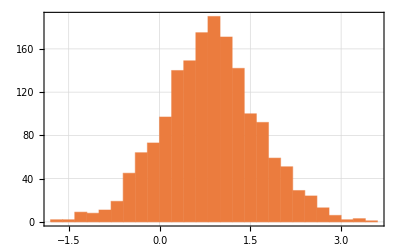
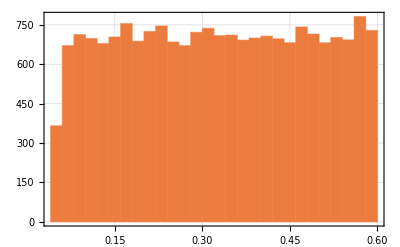
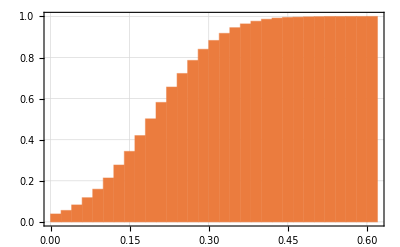
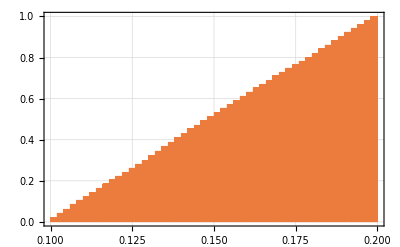
```mathematica
If[family=="None",  famflg=False,famflg=True];
(*If[updateword=="popplot
",update=False,update=True]; ??? *)
explicitfac=1.;
Print["got tohere"];
(*get the asteroid crater count  for the two input files 'Gaspra' and 'Ida' , Eros, Lutetiathe crater counts are listed in files; note the required format, location and name for adding others.  for example, an input file named 'asteroidxx' would have its observed cumulative counts in the file 'asteroidxxcratercum' in the folder 'Asteroid_crater_count_data'*)

If[craters,
explicitfac=0.1; (*;*)  (* a single target runs fast. but plots slow  for ceres...still set the implicit/explicit division very low *)(* but this needs to depend on the target size.  limit the number of explicit? *)

smallest=d0/1000;
If[(newname=="Gaspra"||newname=="Ida"||newname=="Eros"||newname=="Lutetia"||newname=="Ceres"),
Which[
newname=="Gaspra",upscalefac=Pi dmin^2/90,(* Gaspra data is for a 90 km^2 patch *)
             newname=="Ida",upscalefac=Pi d0^2,(* Ida data is per square km *)
newname=="Lutetia",upscalefac=Pi d0^2,(* data is per square km *)
             newname=="Eros",upscalefac=963.,
	newname=="Ceres",upscalefac=Pi d0^2];(* Eros data is per square km use online formula for ellipsoid *)
(*add upscalefac for additional asteroid with observed crater counts here...
It increases the number of craters in the cumulative count of an observed area to the entire surface  Of course, that might miss a few large craters*)
astcraters=Import[FileNameJoin[{dir,"data/Asteroid_crater_count_data",ToString[newname]<>"cratercum"}],"nb"];
astcraters=Transpose[{astcraters[[All,1]],upscalefac astcraters[[All,2]]}];
smallest=Min[astcraters[[All,1]]]
Print["the smallest in the data is ",smallest],astcraters={ }]
(* for other asteroids, need to include name and path here *)

(* these cases run very fast.  to get completeness in the calculated crater count,I decrease the min impactor size for the explicit calcs to a smaller number  Too small and the dynamic plot of the cratering will take a long time *)];


Print["and so on  "];
tmaxby=1. tmaxby;
tmax=tmaxby 10^9;
endtime=tmax;
dlist={};
dmax=Min[dmax,cumdistr[[1,1]]];
dmin=Max[dmin,dialast];
If[dmax≠dmin,exact=False,exact=True];
tumbleangle=tumbleangle˚ Degree;
probi=(velfac*2.85)/10^18;
omegs=Sqrt[(4*(Pi/3)*6.67*dens)/10^20];
nhistplots=Max[1,Min[nhistplots,nasteroids]];

binfirst=astnum[dmax][[2]];
binlast1=astnum[diameterlast][[2]]; (* limit for constant ratio of targets to population *)
binlast=astnum[dmin][[2]];
If[!famflg,ntopick=Table[0,numcum-1]; (* number of test asteroids in each differential bin *)
calcnasteroids[]];  (* finds ntopick *)

ndmin=Round[astnum[dmin][[1]]];
rmin=dmin/2;
rmax=dmax/2;
ndmax=Round[astnum[dmax][[1]]];
massmin=4*(Pi/3)*rmin^3*dens;  (* mass of smallest, largest target *)
massmax=4*(Pi/3)*rmax^3*dens;
velave=velfac*5.29; (* this is used for estimates, the velocity population is used for histories *)

(* these are for the curves of probable largest crater *)
factor=(-Log[(1-prob)])^-(1/alpha0);
probfacs={.9,.63,.5,.3,.10};  (* the probability levels for plotting max expected crater *)
facvals=Table[factor/.prob->probfacs[[i]],{i,5}];
nwanted={1,2,5,10,30,100};

lostfrombins=Which[
depleteword=="Bottke",
Table[depletionbottke[bindias[[i]]],{i,numcum-1}],
depleteword=="Bottke2",
Table[depletionbottke2[bindias[[i]]],{i,numcum-1}],
depleteword=="O'Brien",
Table[depletionobrien[bindias[[i]]],{i,numcum-1}],
depleteword=="O'Brien2",
Table[depletionobrien2[bindias[[i]]],{i,numcum-1}],
depleteword=="Obrienpluspower",
Table[depletionobpluspower[bindias[[i]]],{i,numcum-1}],
depleteword=="None",
Table[0,{i,numcum-1}],
depleteword=="Not Relevant",
Table[0,{i,numcum-1}]];

totaldepletion=Table[0,numcum-1];  (* for totals numbers in each bin *)
depletemasses=Table[0,numcum-1];(* for total depletion masses in each bin *)
lostfromsmallestbin=lostfrombins[[binlast]]; (* from the depletion model *)
(*Print[{binfirst,binlast1,binlast}];*)


(* construct the list of test asteroids unless it is a family *)
If[!famflg,If[exact, dlist=ConstantArray[dmin,nasteroids] ,
(* else a range *)
Do[
Do[(d=RandomReal[{cumdistr[[ibin,1]],cumdistr[[ibin+1,1]]}];
  (* the original diameter of this random target *)
AppendTo[dlist,d];
),ntopick[[ibin]]]
,{ibin,binfirst,binlast}]],
(*else *)
dlist=family0pts]; (* does not use ntopick *)
dmax=Max[dlist];
(* if large ones included add some exact ones. except i dont know the original diameter *)
dlist=RandomSample[dlist]; (* shuffle the order, otherwise all the big ones are first *)

(* LOAD THE astsizetype array for the first timestep *)


astsizetype=Table[{0,0,0,0,0,0,0},{nasteroids}];
(* diameter, type, flag for pinup in transition region,  the value of grav limit,
zeta0, ashape, beta *)

astsizetype[[All,1]]=dlist;  (*initial values in here for safekeeping *)
(* load types*)

If[asttype=="25-75 Mixture",

Do[ntype=RandomInteger[{1,4}];
               If[ntype==1,asttypethis="S-Type",
     asttypethis="C-Type"] ; 
astsizetype[[iast,2]]=asttypethis,{iast,nasteroids} ],

astsizetype[[All,2]]=asttype];

astsizetype[[All,3]]=Table[If[RandomReal[{0,1}]>spinupratio,True,False],{i,nasteroids}]; (* now used to determine a few that can spin past gravlimit between dcenter/3.5, 2 dcenter.*)

(*Table[Max[0,RandomReal[{diaforgravlim,10diaforgravlim}]],{i,nasteroids}];*)
(* here are chances of being grav limited as a function of diametr. the CDF*)
(*-Graphics--Graphics--Graphics-
(* here are chances of being limited as a function of diametr. the CDF*)
-Graphics--Graphics-;*)
(*astsizetype[[All,3]]=Table[diaforgravlim,{i,nasteroids}];*)  (* here all the same *)
gravlim3=gravlimit RandomVariate[TriangularDistribution[{.8,1.02},.95],nasteroids];
(* -Graphics-loads the gravity limit here.  second variable is where the peak is*)
astsizetype[[All,4]]=gravlim3;(*astsizetype[[All,4]]=Table[gravlimit Max[0,RandomVariate[NormalDistribution[1,0.5]]],{i,nasteroids}];*)
astsizetype[[All,5]]=Table[If[astsizetype[[i,2]]=="C-Type",0.4 zetafactor,0.8  zetafactor],{i,nasteroids}];
(* shape parameters *)
astsizetype[[All,6]]=Table[RandomReal[{.8,1}],{i,nasteroids}];
astsizetype[[All,7]]=Table[RandomReal[{astsizetype[[i,6]],1}],{i,nasteroids}];
iiplot=0;(* number and flag for history plot *)
 (* astsizetype loaded *)

cd=cd0; (* this is used for estimates, it is the starting one, it has popfac in it now.. the bin distribution is used for histories *)

originalmass=massindist[cumdistr0,densbar];


NotebookFind[nb, "runit", All, CellTags];
SelectionEvaluate[nb];
```

### main calculation loop

```mathematica
(*SelectionMove[EvaluationNotebook[],Next,GeneratedCell];*)
(*testpts=Table[{},{ii,nasteroids}];*) (* here for diagnostic use, 
but don't load below for large runs, it creates humoungous files *)
(*testpts=Table[{0,0},{numcum}];*)


t0=AbsoluteTime[];

binaries={}; (* Gaurav: May be for listing the binaries *)
nnbinaries={}; (* Gaurav: May be for counting number of binaries *)
cdevent={}; (* the targets with any cd event *)
firstcdevent={}; (* only the  events when d/d0>.5*)
cdplotpts={}; (* Gaurav: For plotting *)
pulvplotpts={}; (* only for asteroids with history plot *)
binforplots={};
pulvevent={};(* keep dia d0, omeg, time of "pulverized" ones *)
pulvevent1={};(* pulv when m> 0.5 m0 *)

 (*get random asteroids for history plots, no duplicates *)
(*Gaurav: Not for my use creating asteroid sample for the purose of plotting
*) 
histast=RandomSample[Range[nasteroids],nhistplots];
(* load itsahist the histroy plot numbers for all hist asteroids. *)
itsahist=Table[0,nasteroids];
Do[itsahist[[histast[[i]]]]=i,{i,nhistplots}];
lastimptime=Table[0,{nasteroids}];
erodedhmevent={};
If[nframes>0,binformovies=Table[{},nframes+10]];

(* impdia={}; for diagnostics only, it becomes humoungous for larget problems *)
```

```mathematica
halfmevent={}; 
erodedhmevent={};
nutation={};
erodedtozero={};
dcrimdias={}; 
craterdias={};
craterdiasnow={};
spalldias={};
complexdias={};
testarray={};
craterplotpts={{0,{{0,1}}}};
totalnow=0;
nexplicit=0;

diffplots={}; 
(* might be better to pick at least one asteroid from each bin for plotting*)
 (* now 3 components the initial values *)
histplotpts=Table[{},nhistplots];


(* load initial histplotpts (for hist targets) *)

runboxplots=Table[{},{i,nsteps+1}];

omegvals=initialspins[]; (* this gets all nasteroids of them *)

(* load  initial history plots. jj is the history plot number, 
    histast[[jj]] is the asteroid number*)
(*Gaurav: Not for my use. It is creating asteroid sample for the plots
*)
 Do[
  omeg=omegvals[[histast[[jj]]]];
  omegzz=Sign[omeg[[3]]] Max[Abs[omeg[[3]]],10^-9];
  wobble=ArcTan[Sqrt[(omeg[[1]]^2+omeg[[2]]^2)]/Abs[omegzz]];
If[Im[wobble]>0,Print["here 3, wobble not real "];Abort[]];
If[wobble<1. Degree, wobble=1.Degree];
  omegnet=Sign[omeg[[3]]] Norm[omeg];
histplotpts[[jj]]={{0,dlist[[histast[[jj]]]],omegnet,wobble}},
{jj,nhistplots}];
(*Gaurav: Storing frames for the movies 
*)
If[nframes>0,asterdata=Table[{},nframes+1]; (* includes first and last  *)
(*asterdata[[1]]=Table[{dlist[[i ]],RandomChoice[{-1.,1.}]omega0},{i,nasteroids}];*)
asterdata[[1]]=Table[{dlist[[i ]],Norm[omegvals[[i]]] 1.38 10^4},{i,nasteroids}]; (* first frame at t=0 *)
nmovie=1; (* counter for data for movie frames *)
framefreq=Max[1,Ceiling[nsteps/nframes]],
(* else *)
framefreq=0;nmovie=0];

(* diagnostics for mass losses *)(* Gaurav: Not for my use *)
sumpop={0,0,0,0,0};
testplot=Table[sumpop,{i,5}];
keepbin={10,20,30,40,50};
percentchange=sumpop;
masstest={};

time=0;
timetonow=0.;

Print["ready to take time steps "];

iiast=0;
iistep=1;
impacttime=10. ;(* need for first monitor output *)
timetonow=0.;
(*maximpd=0;*)
testmaxd={};
testmeanv={};
fragpart=Table[Table[0,numcum-1],{3}] ; (* now 3 types *)
stepdepletion=Table[0.,numcum-1];
 depletepart=Table[0.,numcum-1]; 
numcd=0;
```

```mathematica
Monitor[ 
(* A.  The time steps, {istep,nsteps} *)

(*Initialization codes written by G:*)

parameters=Import["/Users/kumargaurav/Documents/Asteroids/parameters"];
SetDirectory["/Users/kumargaurav/Documents/Asteroids/output"];
mydir=StringJoin["files_",ToString[NumberForm[parameters[[Position[parameters,"delta"][[1,1]]]][[2]]*1.0,{2,6}]],"_",ToString[NumberForm[parameters[[Position[parameters,"omega_initial"][[1,1]]]][[2]],{2,6}]]];
If[DirectoryQ[mydir], DeleteDirectory[mydir, DeleteContents->True],Print["No directory exist"]];
CreateDirectory[mydir];
SetDirectory["/Users/kumargaurav/Documents/Asteroids"];
RegisterExternalEvaluator["Python","/Users/kumargaurav/opt/anaconda3/bin/python3"];
If[FailureQ[parameters],Print["Failed in importing the data"]; Abort[]];
session= StartExternalSession["Python"];
d = astsizetype[[1, 1]]; 
Mkg = Pi/6 dens d^3;
jinertia=2/5 Mkg (d/2)^2  {1,1,1};
parameters[[Position[parameters,"jinertia"][[1,1]]]][[2]]=jinertia[[3]]/(d/2)^5/dens;
parameters[[Position[parameters,"jinertia1"][[1,1]]]][[2]]=jinertia[[1]]/(d/2)^5/dens;
parameters[[Position[parameters,"radius"][[1,1]]]][[2]]=1;
parameters[[Position[parameters,"slides"][[1,1]]]][[2]]=1;
parameters[[Position[parameters,"time"][[1,1]]]][[2]]=0;
parameters[[Position[parameters,"omega"][[1,1]]]][[2]]=parameters[[Position[parameters,"omega_initial"][[1,1]]]][[2]];
resultExport=Export["~/Documents/Asteroids/parameters",parameters,"Table","FieldSeparators"->"    "];
If[FailureQ[resultExport],Print["Failed in exporting the data"]; Abort[]];
myomega={};
AppendTo[myomega,{0,parameters[[Position[parameters,"omega_initial"][[1,1]]]][[2]]*(G*4/3* Pi*dens/10^9)^0.5}];

 Do[
  begintime = TimeUsed[]; (* G: Initial time *)

(* Not Important for us :G *)

  If[Max[dlist] < 10^-4,
   Print["Only 10 cm sizes remain, Nothing more to calculate.  Time=", N[time/10^9], " Byr"];
   endtime = time;
   Break[]];(* G: Check if all particles are very small *)
  
(* Not important as we are not interested in history plots :G *)

  iistep = istep;(* istep is the counter of the loop : Gaurav  *)
  iiplot = 0;
  timeold = time;
  deltime = tmax/nsteps;  (* time increment in years *)
  time = time + deltime; (* global time in years *)

(* For plotting movies . Not Important :G *)

  If[framefreq > 0, If[((Mod[istep, framefreq] == 0) || (istep == nsteps)),
    nmovie++; plotmovie = True, plotmovie = False], plotmovie = False]; (* time for a movie frame *)
  
(* For population change . Not Important :G *)

  (*reset popchange to only that for this timestep there are now 4 types*)
  popchange =Table[ Table[0., numcum-1],3];
  (*difference values to be accumulated over target hits*)
  memused = N[MaxMemoryUsed[]/10^9];
  memavail = N[MemoryAvailable[]/10^9];
  iiast = 1;
expimpdias={};
nnbinaries=AppendTo[nnbinaries,{time, Length[binaries]}]; (* G: For Binaries only *)
  
  (* B.  the target loop, loops on targets for each time step, inside there is a loop on impactors *)
  
  
  Do[  (* B.  target asteroid loop, {iast, nasteroids} *)		

 iiast = iast;
  impacttime = 0.;   (* Created by :G *)
maximpd=0;

   (* see if this is a history asteroid *)
    plothis = itsahist[[iast]];                        (* now the hist plot number, or 0 if not*)

   d = dlist[[iast]];                                             (*current diameter for this asteroid*)
   d0 = astsizetype[[iast, 1]];                (* initial value  *)

(* Checking if it is too small. Not important  :G *)

   If[0 ≤ d < 0.0001,(* eroded down to 10 cm*)
       erodedtozerof[]];
     If[d <= 10^-4, Continue[]]; (* d=0  in erodedtozerof[], kicks out if pulverized *)


    prob=probi deltime  d^2/4;                     (* To be used for calculating number of collisions: G*)

   (* get rest of target properties for this target and time step *)

   asttypestuff[astsizetype[[iast, 2]]]; (* loads properties for c-type or s-type *)
 spinupflg = astsizetype[[iast, 3]]; (* flag for spinup in transition region values set in initialization *)
   gravlimhere = astsizetype[[iast, 4]]; 
   zeta0 = astsizetype[[iast, 5]];
   ashape = astsizetype[[iast, 6]];  (* r is always the averaged *)
   beta = astsizetype[[iast, 7]];
   Y = Y0 (d0strength/(2 r))^(1/nsize); (* G: For Cratering *)
   (* these are the values at the beginning of the impactor loop, they are modified in the loop as erosion happens *)

(* Written by :G *)

   r = d/2;
epsilon=parameters[[Position[parameters,"epsilon"][[1,1]]]][[2]]; (* By G *)
layers=parameters[[Position[parameters,"layers"][[1,1]]]][[2]]; (* By G *)
   Mkg = Pi/6 dens d^3;
   (*jinertia = Mkg/5 r^2 (ashape beta)^-(2/3) { ashape^2 + beta^2, 1 + ashape^2, 1 + beta^2  };*)
   jinertia[[3]]=parameters[[Position[parameters,"jinertia"][[1,1]]]][[2]]*r^5*dens;
  jinertia[[1]]=jinertia[[2]]=parameters[[Position[parameters,"jinertia1"][[1,1]]]][[2]]*r^5*dens;


   dstarave = qstarf[r, Pi/4, velave ][[3]];                                   (* note that this changes in the impactor loop since r changes *)   
   grav = 2 Pi/3  6.67 10^-20 dens 2 r;
   vesc = Sqrt[8 Pi/3 dens Grav] r;
   dgrav = 7.158 10^18 (d0strength/r/2)^(1/nsize) Y0/(dens^2 r);
    (* cratering strength gravity transition.. *)
   masslost = 0;

(* initializing the Omega: G *)

   omeg = omegvals[[iast]]; (*3 components *)
   
(*Finding the bin numbers :G *)

   binnumt = astnum[d][[2]];(* the current bin number *)
   binnumt0 = astnum[d0][[2]];(* the original bin number *)
   
(* Not Important: G *)

   If[MemberQ[binaries[[All, 1]], iast], itsabinary = True, itsabinary = False];
(* the tratio is defined for the target. *)
(* these are the ratios for reducing number in impactor bins for the current target *)
   If[ntopick[[binnumt0]]==0,Print["tratio=? ",{binnumt0,diffdistr[[binnumt0,2]]ntopick[[binnumt0]]}];
Abort[]]; 
tratio=diffdistr0[[binnumt0,2]]/ntopick[[binnumt0]]; (* factor for sampling considerations *)(* G: Can't understand what this tratio implies *)
(* actually not needed for a given set of diameters, i.e. a 'family'*)



(* C. get ready for the impact loop, load the set impactorstuff for each impactor, explicit and implicit. here there is one target and the timestep deltime is set*)
(* i need range or explicit and implicit *)

impactorstuff = {};
dstarave=qstarf[d/2,Pi/4,velave][[3]];
kkk=probi deltime (d/2)^2;

(*Finding number of explicit impactors: G *)

numgtd=astnum[dstarave][[1]];                                 (* number greater than the target *)(* Changed by G. Earlier it was d. *)
dialittle=cumdistr[[80]][[1]];                                             (* second from end. Smallest impactor possible: G *)
If[1/kkk<dialittle,Print["oops, 1/kkk<dialittle",{1/kkk,dialittle }];Abort[]];                                                       (* G: May be to check whether there is even a single impact *)
dexplicit= Max[dialittle, 0.05 explicitfac (dstarave)] ;                                                                                                         (* G: Defining diameter for the explicit limit *) (* Changed by G. Earlier it was 0.1 *)
(*modify for too many as for small targets *) 
(* and need to lower for large targets, especially for lots of time steps or it will get 0 explicit. *)
binexplicit=astnum[dexplicit][[2]];
dexplicit=boundaries[[binexplicit+1]]; (* lower the diameter to the next boundary down *)
nstepexplicit=astnum[dexplicit][[1]];  (* all objects in that range  this must be limited for small targets ? *)
If[nstepexplicit<1/kkk,dexplicit=getdiaf[1/kkk];nstepexplicit=1/kkk];

nexpimpactors=Round[kkk nstepexplicit];(* for small numbers, this can round down to 0  !! *)
(* keep all in this bin, move bdry dia down *)

Print[{nexpimpactors,deltime,kkk,dexplicit,nstepexplicit,dstarave,dialittle,explicitfac, velave,d,densi}];

nexplicit=nexplicit+nexpimpactors;  (* total to here *)
dimplicit=Max[dialast,0.05  dexplicit];                                             (* Changed by G to 0.05. Earlier it was 0.1 *)
(* lower  limit for implicit dont need numbers, only bins *)
binimplicit=astnum[dimplicit][[2]];

(* Finding diameters of explicit impactors :G *)

vec=RandomReal[{numgtd,nstepexplicit},nexpimpactors];
(*dias=InverseFunction[cumfit[vec]];  hangs up sometimes*)
(*dias=ReverseSort[(cdx/vec)^(1/alphax)]; using the approximate power law*)
dias=getdiaf[vec]; (* the set of random explicit impactors  this uses the actual cumdist, with a power law fit over each bin. different for large targets*)
expimpdias=Join[expimpdias,dias];

(* Generating attributes for the impactors :G *)

Do[
 phival = ArcCos[1 - 2 RandomReal[]]/2;
 vel = velstatf[RandomReal[]];
   If[RandomInteger[{1, 4}] == 1, densi = 2.5 10^12, densi = 1.5 10^12]; 
 impacttime = RandomReal[{time - deltime, time}];
thetaval = 2 Pi RandomReal[];                        (* range from 0 to 2 Pi *)
Thetaval = 2 Pi RandomReal[];                       (* location on sphere, range from 0 to 2Pi *)
 Phival = ArcCos[1 - 2 RandomReal[]]; (*range from 0 to Pi*)
  If[dias[[jj]] < dgrav, vstar = k2s Sqrt[Y/dens] ,(*else*) 
         vstar = k2g vel Cos[phival] (grav diameter/2/(vel Cos[phival])^2)^(1/(mu + 2)) ];
 
AppendTo[impactorstuff, {dias[[jj]], phival, vel, densi, 1,impacttime, vstar, thetaval, Phival, Thetaval}];
,{jj,nexpimpactors}] ;   

(* now append the implicit ones, only one for each bin  *)
If[binimplicit>binexplicit,
Do[
ninbin=Round[kkk diffdistr[[jj, 2]]];(* number of impactors in this implicit bin *)
diameter = Exp[(Log[cumdistr[[jj, 1]]] + Log[cumdistr[[jj + 1, 1]]])/2];         phival = Pi/4.;
        vel = velave;
        If[RandomInteger[{1, 4}] == 1, densi = 2.5 10^12, densi = 1.5 10^12];
        impacttime = RandomReal[{time - deltime, time}];
        thetaval = Pi; (* doesn't matter *)
        Thetaval = 0.;
        Phival = Pi/2;(* doesn't matter *)
        If[diameter < dgrav, vstar = k2s Sqrt[Y/dens] ,(*else*) 
         vstar = k2g vel Cos[phival] (grav diameter/2/(vel Cos[phival])^2)^(1/(mu + 2)) ];
        AppendTo[impactorstuff, {diameter, phival, vel, densi,ninbin, impacttime, vstar, thetaval, Phival, Thetaval}];
,{jj,binexplicit,binimplicit-1}]];

 (* i now have the impactors, now mix them up and do impacts *)
   
   (* load the impactors list for this time step *)
          
impactorstuff = Sort[impactorstuff, #1[[6]] < #2[[6]] &];                            (* sort impactors by time values *)
   
   
   (* E.  2nd impactor loop, over the list of explicit and implicit impactors *)
   
   vellist={};

(* My codes: G *)

G=6.67*10^(-11);
omeg[[3]]=parameters[[Position[parameters,"omega"][[1,1]]]][[2]]*(G*4/3* Pi*dens/10^9)^0.5;
obliq= parameters[[Position[parameters,"obliq"][[1,1]]]][[2]];
time0=time-deltime;
slides=1;
   Do[                                                                                            (* {ii,Length[impactorstuff]} loop over impactors in time order  *)
   
    If[d/d0 < .001,(* Print["break since d/d0<.001 "];*)Break[]];(* it busted.forget the rest of the impactors. *)
    
    diameter = impactorstuff[[ii, 1]];
   
   If[diameter<10^-5,Break[]]; (* but this should not happen?? *)
binnumi = astnum[diameter][[2]]; (* this could be carried along, not reconstructed..  *)

    phival = impactorstuff[[ii, 2]];
    vel = impactorstuff[[ii, 3]];
AppendTo[vellist,vel];
    densi = impactorstuff[[ii, 4]];
    ninbin = impactorstuff[[ii, 5]];
   impacttime = impactorstuff[[ii, 6]]; (* time when this impactor hits *)
    
    tlasthit = If[ii > 1, impactorstuff[[ii - 1, 6]], time - deltime];                                              (* time when previous impactor hit this target *)
    
    vstar = impactorstuff[[ii, 7]];
    thetaval = impactorstuff[[ii, 8]];
    Phival = impactorstuff[[ii, 9]];
    Thetaval = impactorstuff[[ii, 10]];
    mass = Pi/6 densi diameter^3;
    
    dlast = dlist[[iast]];                                                                                                (* current target d in impactor loop *)
    
    trelax = relaxfac Log[wobble/(1. Degree)]/2  1.1 10^-3 dlast^-2 Abs[omegnet]^-3;  

    (* new trelax in years, manuscript Eq. 41,  for any initial and adjusted to 1 degree *) 
    (* these have to be here since d and omeg are changing *)
    
    qstar = qstarf[dlast/2, phival, vel][[1]];
    (*qq = (mass/2) (vel Cos[phival])^2/Mkg; *)
   qq = (mass/2) (vel )^2/Mkg; 
    qratio = qq/qstar;

omegaLimit=(G*4/3* Pi*dens/10^9)^0.5;                                                (* Omega limit derivec by me for the spherical case ;G *)

(* My Codes :G *)

Yorp[];

(*Print[impacttime];*)




outcomesf [];                                                                                                 (* primary calculation of each impact, gives new d, calls dmeg to get omeg *)
Print["Omega after the collision",omeg[[3]]];
AppendTo[myomega,{time0,omeg[[3]]}];
(* MY CODES for coupling *)

If[diameter>dexplicit,

Landslides[];
Print["Omega after the Landslides",omeg[[3]]];
];
time0=impacttime;

(*MY CODES  end *)

    (* now check if it became a overspun candidate *)

    currentspinlim = combinedspinlimf[d, dcenter, gravlimhere, spinupflg];
    If[Norm[omeg] > currentspinlim, spunoverf[] ];                                                                     (* will update omeg, set wobble to zero (1˚) if spunover *) (* G: spunoverf changed by me *)
    (* now load all new values *)
     dlist[[iast]] = d;  (* new reduced diameter *)
     omegvals[[iast]] = omeg;(* current value  3 components *)
    omegnet = Sign[omeg[[3]]] Norm[omeg];
    
    
    omegzz = Sign[omeg[[3]]] Max[Abs[omeg[[3]]], 10^-9];
    wobble = ArcTan[Sqrt[omeg[[1]]^2 + omeg[[2]]^2]/Abs[omegzz]];

If[Im[wobble]>0,Print["here 4, wobble not real "];Abort[]];
If[wobble < 1. Degree, wobble = 1. Degree];
    
    If[ plothis > 0, (* keep track of all hits for a history asteroid, plothis is the history plot number *)
     AppendTo[histplotpts[[plothis]], {impacttime, d, omegnet, wobble}]];
    
    (* now reduce size of remaining impactors to account for reduction in target size, w/o recalculation all the impactor. 
    max expected scales like dlargets~d^(2/alpha), but alpha~2.04 
    so largest espected dlargest->d, *)
    If[d/dlast < .95,
     Do[impactorstuff[[ij, 1]] = impactorstuff[[ij, 1]] d/dlast;, {ij, ii + 1, Length[impactorstuff]}]]
    
    , {ii, Length[impactorstuff]}];

   (* end of impactor loop all impacts for this target and time step *)
   
   (* end of time step  make history plot for this target? relax wobble, add end time step history points..*)
    (* get last relaxation*)
   
 
   impacttime = time;
Yorp[];
   calcomega[0];  (* relax spin to final time, no new impacts *)
   omegvals[[iast]] = omeg;
resultExport=Export["~/Documents/Asteroids/omega_1",myomega,"Table","FieldSeparators"->"    "];
If[FailureQ[resultExport],Print["Failed in exporting the data"]; Abort[]];   


   (*If[ plothis>0,
   AppendTo[histplotpts[[plothis]],{time,d,omegnet,wobble}]];*)
   If[plotmovie, AppendTo[asterdata[[nmovie]], {d, Norm[omeg] 1.38 10^4}];
    (*Print["adding to asterdata",{nmovie,iast}];*)
    If[itsabinary, AppendTo[binformovies[[nmovie]], {d, Norm[omeg]}]]];
   
   
   (* reload shapes for next go-round *)
   astsizetype[[iast]][[6]] = ashape;
   astsizetype[[iast]][[7]] = beta;
  
   , {iast, nasteroids}];
  
    (* end of target asteroid do loop still in time step loop*)
  (* here i have looped on all test asteroids for this time step *)
  
  (* get run box mean spins for each time step of remaining asteroids
  do not need to cull out the zero cases, that is done in runboxmeanf[] *)
  (* get run box mean spins for each step *)
  
If[Min[dlist]<0.9 Max[dlist]&&Length[dlist]>6,
     spinptsnow = Table[{dlist[[i]], 1.38 10^4 Norm[omegvals[[i]]]}, {i, Length[dlist]}];
   meanplot = runboxmeanf[spinptsnow, 1.1, Green];
meanplot=ListLogLogPlot[{{Mean[dlist], 1.38 10^4 Norm[Mean[omegvals]]}},PlotStyle->Green];
   
   runboxplots[[istep]] = Show[meanplot, spindata2019means, spinlimplots["Cycles/day"],
     Graphics[Text[Framed[StringForm["This is the running box mean of the target asteroids\r at `` Yrs.\rThe red curve 
         is from the spin database: \rThe left segment is from NEA's, \rthe right segment is the main belt", N[time]]],
       Scaled[{.4, .15}], Background -> White, BaseStyle -> {14, FontFamily -> "Times"}]], ImageSize -> Full]];
(* running box mean *)
  
  (* can now update cumdistr and number in each bin*)
  (* the depletion is a given rate as a function of dia, scale by time step size *)
  (* now the change due to fragmentation in each bin *)
  
  (* F.  update POPULATIONS after the target loop and at end of each time step *)

(* Comments on mass adjustments ; *)
(*  The additions and losses to the differential distribution, the number in each bin, for the impacts are divided into 3 parts.  The array 'popchange[[i]]' for each of 3 parts is the changes in numbers in each bin and is reset to zero at the beginning of the time step. It is accumulated for each target and its impacts. at the end of the time step, it is added into diffdistr whihc are the pairs of diameters and numbers.

The 3 parts include loss of impactor and target, and gain of fragments.  They are:  
 1.  The loss including th impactor and redistribution from cratering (ignored?). popchange[[1]]
2. The losses and redistribution for near or over CD event from a target in a bin. popchange[[2]]
3. The losses and redistribution from a pulverization, includes impactor, from a target in a bin. popchange[[3]]

In each case each target is considered a sample from each bin. Therefore the total associated with each event is multiplied by the ratio of the total number of targets in a bin to the number of sample targets in the bin.

The 3 impact events are considered first, and then the depletion.
Note also that the diffdistr is the number of objects in each bin, the corresponding mass is caculated separately using massindist[dist_,densbar_].*)

  If[!steadypop,
  (* accumulate frag during time steps for each bin. now there are 3 kinds *)
fragpart=fragpart+popchange; (* the total bin numbers of 3 types of changes of frags at the end of each time step.  used for plotting, either movies or at end *)
(*Print["update populations here {time,istep,popchange,fragpart",{time,istep,popchange,fragpart}];*)

popchangeall=Sum[popchange[[ik]],{ik,3}]; (* all 3 types combined *)
(* accumulate all changes for diffdistr*)

diffdistr[[All, 2]]=Table[Max[0,diffdistr[[ii,2]]+popchangeall[[ii]]],{ii,numcum-1}];
(* cannot remove more than all of them.. *) (*diffdistr[[All, 2]]=diffdistr[[All,2]]+popchangeall[[All]];*) (* what if negative?*)
(*Print["huh2? ",diffdistr];*)

(* now the depletions *)
difflossrate = lostfrombins diffdistr[[All, 2]]; (* number rate lost from each bin per million year.  some percentage of remaining oness*)
stepdepletion =(tmax/nsteps)/10^6 difflossrate;(* number lost in this time step from each bin from depletions *)
(*Print["time, depletions ",{time,stepdepletion}];*)
(*make a cumulative number distribution of all to this time step.. to here the depletions are positive. *)
(* Print["accumulate2 ",{time,diffdistr[[31,2]],stepdepletion[[31]]}];
*)
depletepart=depletepart+stepdepletion; (*total numbers to this time *)

(*this should never be needed.. diffdistr[[All, 2]] =Table[Max[0,diffdistr[[ii,2]]-stepdepletion[[ii]]],{ii,numcum-1}]; 
*)
diffdistr[[All, 2]] =diffdistr[[All,2]]-stepdepletion[[All]]; (*Print["accumulate3 ",{time,diffdistr[[31,2]]}];*)

cumdistr = Transpose[{cumdistr0[[All, 1]], Prepend[Accumulate[diffdistr[[All, 2]]], 0]}];
     

(* these are for movies of population *)

cumplots[[istep+1]]= Show[cumplot1,cumplot2,ListLogLogPlot[cumdistr, ImageSize -> Large,PlotStyle->Black,Joined->True,
      PlotRange -> {{10^-5, 10^3}, {.1, 10^16}}], Graphics[Text["Time= " <> ToString[time/10^9]<>" Gyr", Scaled[{.5, 0.9}]]]]];

(*AppendTo[diffplots, Show[ListLogLogPlot[diffdistr, ImageSize -> Large, PlotRange -> {{10^-4, 10^3}, {.1, 10^16}}],
     ListLogLogPlot[Transpose[{cumdistr[[All, 1]],- Sum[fragpartcum[[ii]],{ii,4}]}], PlotMarkers -> "f", ImageSize -> Large,
      PlotRange -> {{10^-4, 10^3}, {.1, 10^16}}], Graphics[Text["Timestep= " <> ToString[itime], Scaled[{.5, 0.9}]]]]];
  
 ];*) (*end of not steady update..*)

  calctime=AbsoluteTime[];
  astsurv = Flatten[Position[dlist, _?(# > 1. 10^-5 &)]]; (* all with d>10^-5 *)
  
  If[craters && d > 0,
   (* now upscaled to the entire asteroid surface area, next get all calculated craters to date *)
   craterdias = Join[spalldias[[All, 3]], dcrimdias[[All, 3]], complexdias[[All, 3]]];
   craterdias = ReverseSort[craterdias]; (* for distibutions *)
   plotpoints = Transpose[{craterdias, Range[Length[craterdias]]}];
   AppendTo[craterplotpts, {time + deltime, plotpoints}](* these are all of the craters to this time. *)
   ];
  
  dtimetonow = N[AbsoluteTime[] - t0] - timetonow;
  timetonow = N[AbsoluteTime[] - t0];
  

  , {istep, nsteps}],

 (* For Output Screen: G *)
 
 numastdone = (iistep - 1) nasteroids + iiast;
 totaltimeestimate = (nasteroids nsteps/numastdone) timetonow;
 timetogo = totaltimeestimate - timetonow;

 If[timetonow == 0.,  
   timetogomin = expecttime/60,
   timetogomin = timetogo/60];
 
timetogohr = timetogomin/60; 
 
 string1 = Style[DateString[localtime0] <> ". \nSSAH Version " <> ToString[mversion] <> ".\n", {Large, Red}];
 string1a = StringForm["Timestep `1` of `2`", iistep, nsteps];
 (*Print[{iistep,nsteps,iiast,impacttime,numastdone,timetonow,timetogo,totaltimeestimate}];*)
 {string1, string1a,
  ProgressIndicator[Dynamic[(iistep/nsteps )], ImageMargins -> 10, Background -> Red],
  
  Framed[Style[StringForm["Current Problem Time `` years of `` total,  Elapsed Computer Time `` seconds or `` minutes", 
  NumberForm[time, {5, 1}],NumberForm[tmax, {4, 1}] , NumberForm[timetonow, {4, 1}],NumberForm[timetonow/60., {4, 1}]], 16], Background -> LightBrown],
  If[bornagain, Nothing, Framed[Style[StringForm[" Asteroids Surviving ``", 
      NumberForm[If[iistep==1,nasteroids,Length[astsurv]], {4, 0}]/nasteroids], 16], Background -> LightYellow]],
  (*Framed[Style[StringForm[" Number of tumblers ``", NumberForm[Length[tumblers],{3,0}]/nasteroids],16],
  Background->LightYellow],*)
  Framed[Style[StringForm[" Estimated Time Remaining `` minutes, (`` hours)" ,
     NumberForm[timetogomin, {4, 1}], NumberForm[timetogohr, {5, 3}]], 16], Background -> LightBlue],
  Framed[Style[StringForm[" Memory used `` GB, Available: `` GB .. \r(Reruns do not release memory.  
     To free up memory, quit and restart kernel from menu item ...)"
     , NumberForm[ memused, 2], NumberForm[ memavail, 2]], 16], Background -> LightPurple]
  }
Clear[session];
 ];
(* end of monitor  *)


(*Speak["The calculation is finished, should I construct the plots?"];(*)//RuntimeTools`Profile*)*)
test = ChoiceDialog["Do you want
   me to make the plots of output?", {Yes -> 1, No -> 0}];
If[test == 1, NotebookFind[nb, "outcell", All, CellTags];
 SelectionEvaluate[nb], NotebookFind[nb, "firstone", All, CellTags]; Abort[]];
```

```mathematica
time0
```

```mathematica
(* now all of the output *)
  (* now all of the output *)
  (* now all of the output *)
     (* now all of the output *)
(*FrontEndTokenExecute["DeleteGeneratedCells"];*)(*take out, dumps input cell stuff and disgnostics*)

TextCell[outtext, "Title", CellFrame -> True, FontSize -> 16, Background -> LightGreen];

Row[{"Constructing the Figure " ,Dynamic[ToString[xdone]],"    ",
ProgressIndicator[Dynamic[xdone],{0,13},BaseStyle->Large]}]


(*MessageDialog[Row[{"Constructing the Figure " ,Dynamic[ToString[xdone]],"    ",
ProgressIndicator[Dynamic[xdone],{0,11},BaseStyle->Large]}]]*)

colors=Join[{Black,Red,Blue,Green,Purple,Yellow},RandomColor[nhistplots]];
(* always output a summary slide *)
(* all remaining *)
fulltermd = dlist[[astsurv]];  (* strips zeroes *)
finalomegs = omegvals[[astsurv]];
numleft = Length[fulltermd];
If[numleft>0,dsmallest= Min[fulltermd];
dlargest = Max[fulltermd];
enuf=(numleft>20&&dlargest/dsmallest>2);,
(*else*)
dsmallest=0;
dlargest=0;
enuf=False;]
 
If[numleft > 0,
  fulltermnet = Table[Norm[finalomegs[[i]]], {i, numleft}]; (* the norms, all positive here *)
  fulltermwobble = Table[ArcTan[Sqrt[(finalomegs[[i, 1]]^2 + finalomegs[[i, 2]]^2)]/Abs[finalomegs[[i, 3]]]], {i, numleft}]; (* the wobbles, all are wobbling to some radian *)
  maxspin1 = Max[fulltermnet];
  minspin1 = Min[fulltermnet];
  spinpts = Transpose[{fulltermd, 1.38 10^4 fulltermnet}];  (* for fig 1 *)
  (* lets get the number and lsit of those above, say, 15˚ *)
test = Position[fulltermwobble, _?((# > tumbleangle) &)] // Flatten;
  numtumblers = Length[test]]; 

maxhistspin = Max[Abs[histplotpts[[All, All, 3]]]];
numpulv = Length[pulvevent];
numcd = Length[cdevent];
numpulvplots = Length[pulvplotpts];
numtozero = Length[erodedtozero];

(* binaries *)
binarylist = binaries[[All, 1]];  
If[Length[binarylist] > 0, binariestoplot =Transpose[{dlist[[binarylist]], Table[Norm[omegvals[[binarylist[[i]]]]], {i, Length[binarylist]}]}]; (* current state of binaries *)
  numbin = Length[binarylist]; (* the surviving binaries *)
  numbinplots = Length[binforplots],
  numbin = 0;
  numbinplots = 0;];

(* CD events *)
numcd = Length[cdevent];
numfirstcdevent = Length[firstcdevent];
numhalf = Length[halfmevent];
numhalferoded = Length[erodedhmevent];

meanhalfmass = Mean[halfmevent[[All, 3]]];
medianhalfmass = Median[halfmevent[[All, 3]]];
periods = 2 Pi/fulltermnet/3600;
(*Print["peroids =",periods];*)
medianperiod = If[Length[periods] > 0, Median[periods]];


outtext = ToString[string1] <> ToString[descript] <> "\r" <> "\n● The simulation for " <> ToString[nasteroids] <> " " <> ToString[ asttype] <> " asteroids, with diameters from " <> ToString[dmin] <> " km to " <> ToString[dmax] <> " km is done; \n● There were " <> ToString[Round[nexplicit]] <> " explicit impacts, an average of " <> ToString[N[Round[nexplicit/nasteroids]]] <> " per target.; \r● The calculation took " <> ToString[Floor[ calctime - t0]] <> " seconds (" <> ToString[N[(calctime - t0)/60, 3]] <> " minutes;)" <> " compared to the expected estimate of "<>ToString[N[expecttime/60]]<> " minutes, and used " <> ToString[N[MemoryInUse[]/1000000000, 3]] <> " GB of memory." <>
   "\n" <>
   If[bornagain, "\n\nBut since they were reborn after each destruction along the way,  \n\t●  All of the original " <> ToString[nasteroids] <> " survived to the time of " <> ToString[N[endtime/10^9]] <> " Byr; \n\tThe simulation was to run for " <> ToString[N[tmax/10^9]] <> " Byr.\n\n", "\n\t● " <> ToString[numleft] <> "/" <> ToString[nasteroids] <> " of the original " <> ToString[nasteroids] <> " survived \r\t  to the time of " <> ToString[N[endtime/10^9]] <> " Byr; The simulation was to run for " <> ToString[N[tmax/10^9]] <> " Byr.\n\n"] <>
   
     "\t● The Number of Catastrophic Events (not including pulverized) that occurred  was \n\t  " <> ToString[ numcd] <>  "/" <> ToString[nasteroids] <> ". Of that number, " <> ToString[numfirstcdevent] <> " were before erosion to below half mass,\n\tthe rest were subsequent or after being reborn;\n\n" <>
   
   "\t● The Number of Asteroids Reduced to less than Half-mass by Erosion\n\t    alone was " <> ToString[numhalferoded] <> "/" <> ToString[nasteroids] <> ";" <>
      "  In addition, " <> ToString[numtozero] <> " were eroded to essentially zero size;\n\n"  <>

   "\t● The Total Number of Asteroids Reduced to less than Half-mass by Erosion,\n \t CD Event, or Pulverization was " <> ToString[numhalf] <> "/" <> ToString[nasteroids] <>
   ";\n\n" <>
   
  "\t● The Total number of pulverizations occurring was " <> ToString[ numpulv] <> "/" <> ToString[ nasteroids] <> " many after a previous CD;\n\n" <>
   
  "\t● The number of asteroids with  Gravity Limit Excursions by the end of the simulation \n \t was  " <> ToString[ numbin] <>  "/" <> ToString[nasteroids] <> " or " <> ToString[NumberForm[100. numbin/ nasteroids, {3, 1}]] <> " percent;\n\n" <>
   
        If[numleft>0,  "\t●  The number wobbling at greater than " <> ToString[tumbleangle˚] <> " ˚ at the end of the simulation \n \t   was  " <> ToString[ numtumblers] <>  "/" <> ToString[numleft] <> " or " <> ToString[NumberForm[100. numtumblers/ nasteroids, {3, 1}]] <> " percent;\n", " "];

outtext2 = "\r\t● Although tmax was set at " <> ToString[N[tmax/10^9]] <> " Byr, \n\tThe calculation terminated at time of " <> ToString[N[endtime/10^9, 3]] <> " Byr because no targets remained;  \n\t
      The actual number of explicit impacts per target was " <> ToString[nsteps endtime/tmax] <> ";\n\n";

outtext3 = "\n\n\t☺ (but they were replaced along the way).";


 If[endtime < tmax, outtext = outtext <> outtext2];
If[bornagain, outtext = outtext <> outtext3];

textonplots = Graphics[Style[Text[Framed[plottext, Background -> LightRed], Scaled[{.98, .98}], {1, 1}],14]];

TextCell[outtext, "Title", CellFrame -> True, FontSize -> 16, Background -> LightGreen]



(* now the plots...*)
popplotf[] 

CellPrint[Cell[ToString[StringForm["Figure 0.  The black dashed curve is the original cumulative number population of asteroids, the black solid one is the current population. The blue one is a possible goal for the evolution of the population. The lower green one is the initial distribution of `` target asteroids.  The red plot and right scale are the masses in each bin of the population.",nasteroids]],"Text",Background->GrayLevel[.9]]];
Print["===================================================================================="];

If[!steadypop&&nframes>0,
ListAnimate[cumplots,AnimationRepetitions->2,AnimationRunning->False,ImageSize->Full,DisplayAllSteps->True]]

If[!steadypop&&nframes>0,CellPrint[Cell[ToString[StringForm["Figure 0.1. A movie of the Population History ",nhistplots,nasteroids]],"Text",Background->GrayLevel[.9]]];
Print["==============================================================================================="]]

(* provisions to compare inital target dist, final target dist and actual data if data is a given set *)

(*If[famflg,data=Table[{i,family0pts[[i]]},{i,nasteroids-1}];fam0plot=ListLogLogPlot[data,PlotStyle->Black,PlotMarkers->{"•",Tiny},PlotRange->{{.1,10^5},{.001,1000}}];
ddlist=ReverseSort[dlist];
data2=Table[{i,ddlist[[i]]},{i,nasteroids-1}];
famnowplot=ListLogLogPlot[data,PlotStyle->Red,PlotMarkers->{"•",Tiny}];
data3=Table[{i,notshiftedpts[[i]]},{i,nasteroids-1}];
famdataplot=ListLogLogPlot[data3,PlotStyle->Green,PlotMarkers->{"•",Tiny}];
Show[fam0plot,famnowplot,famdataplot]]*)

(* get better initial estimate*)
(*If[famflg,
familythenpts=2 notshifted-famnowpts;
famthenplot=ListLogLogPlot[familythenpts,PlotStyle->Green,PlotRange->{{.001,1000},{1,2 10^4}},FrameLabel->{"diameter, km","number greater than"}]; turn this on and plot it to get a better estimate for the starting population.*)

(* now a plot showing the mass loss from each of 4 types using popchange, plus the depeletion which was put into diffdistr directly *)

(* get all types of bin masses *)

If[!steadypop,massdistplots[];
DynamicModule[{names2},
Manipulate[
Show[
Which[
names2=="All",{plotmass0,plotmassf,plotlost,plotgained,plotdeplete,plotpulvgain,plotpulvloss,plotcdloss,plotcdgain,plotcratergain,plotcraterloss},

names2=="Original, final and net losses and gains",{plotmass0,plotmassf,plotlost,plotgained},

names2=="Losses from dynamic depletion",{plotdeplete},names2=="Gains and losses from Near CD",{plotcdgain,plotcdloss},
names2=="Gains and lossses from pulv",{plotpulvgain,plotpulvloss},
names2=="Gains and lossses from cratering",{plotcratergain,plotcraterloss}
],ImageSize->Full,FrameLabel->{"Diameter, km","Mass, kg, in each bin"}],
{{names2,"All",Style["Which Plots?",Bold,14]},
{"All","Original, final and net losses and gains","Losses from dynamic depletion","Gains and losses from Near CD","Gains and lossses from pulv","Gains and lossses from cratering"},ControlType->PopupMenu}]]]

If[!steadypop,
masstable=Grid[{{"MASS ACCOUNTING",SpanFromLeft},

{"Item", "± Total Mass, Kg","Plot Legend","Value for 1 km bin","Value for 100 m bin","Value for 10 m bin","Value for 1 m bin"},

{ "Original Mass", NumberForm[mass0,{4,4}] ,"Black Squares",NumberForm[mass0inbin1,{4,4}],NumberForm[mass0inbin2,{4,4}],NumberForm[mass0inbin3,{4,4}],NumberForm[mass0inbin4,{4,4}]},

{"Final Mass",NumberForm[finalmass,{4,4}],"Black Curve",NumberForm[massfinbin1,{4,4}],NumberForm[massfinbin2,{4,4}],NumberForm[massfinbin3,{4,4}],NumberForm[massfinbin4,{4,4}]},

{"Change, Gain (+), Loss (-); % ",ScientificForm[totallost,{4,3}],"Red Curve ",NumberForm[massdiffinbin1,{4,4}],NumberForm[massdiffinbin2,{4,4}],NumberForm[massdiffinbin3,{4,4}],NumberForm[massdiffinbin4,{4,4}]},

{"Depletion",NumberForm[depletemass,{4,4}],"Red Curve",NumberForm[depleteinbin1,{4,4}],NumberForm[depleteinbin2,{4,4}],NumberForm[depleteinbin3,{4,4}],NumberForm[depleteinbin4,{4,4}]},

{"Pulv masses gained",NumberForm[pulvposmass,{4,4}],"Orange Curve",NumberForm[pulvbingain1,{4,4}],NumberForm[pulvbingain2,{4,4}],NumberForm[pulvbingain3,{4,4}],NumberForm[pulvbingain4,{4,4}]},

{"Pulvmasses lost",NumberForm[pulvnegmass,{4,4}],"Orange Markers",NumberForm[pulvbinloss1,{4,4}],NumberForm[pulvbinloss2,{4,4}],NumberForm[pulvbinloss3,{4,4}],NumberForm[pulvbinloss4,{4,4}]},

{"Near CD masses gained",NumberForm[cdposmass,{4,4}],"Purple Curve",NumberForm[cdbingain1,{4,4}],NumberForm[cdbingain2,{4,4}],NumberForm[cdbingain3,{4,4}],NumberForm[cdbingain4,{4,4}]},

{"Near CD masses lost",NumberForm[cdnegmass,{4,4}],"Purple Markers",
NumberForm[cdbinloss1,{4,4}],NumberForm[cdbinloss2,{4,4}],NumberForm[cdbinloss3,{4,4}],NumberForm[cdbinloss4,{4,4}]},

{"Cratering masses gained",NumberForm[craterposmass,{4,4}],"Blue Curve",NumberForm[craterbingain1,{4,4}],NumberForm[craterbingain2,{4,4}],NumberForm[craterbingain3,{4,4}],NumberForm[craterbingain4,{4,4}]},

{"Cratering masses lost",NumberForm[craternegmass,{4,4}],"Blue Markers",
NumberForm[craterbinloss1,{4,4}],NumberForm[craterbinloss2,{4,4}],NumberForm[craterbinloss3,{4,4}],NumberForm[craterbinloss4,{4,4}]}},

Frame->All,ItemStyle->{Automatic,{Bold,Bold}}];
Print[masstable]]

CellPrint[Cell[ToString[StringForm["Figure 0.5.  The mass change in each bin versus the the bin diameters from two impact types and that lost to dynamic depletion.  The upper black square symbols are the original mass in each bin, the black curve are the final masses. Values shown as green, dashed are the net gain, the green curve are the net losses. The Red curve is the magnitude of the dynamic depletion and gone from the belt. For pulverization impacts, the orange curve are the gains, and the orange ▼ are the loss magnitude. For near-CD impacts, the purple curve are the gains, and the purple ▼ are the loss magnitudes. For cratering impacts, the blue curve are the gains, and the blue symbols are the loss magnitudes."]],"Text",Background->GrayLevel[.9]]]
Print["==================================================================================="];
Print["==================================================================================="]

CellPrint[Cell["I.  Here are the Final States of the Surviving Asteroids","Section",Background->GrayLevel[.7]]];



xdone=1;

If[numleft>0,
DynamicModule[{tangle,names2,unitsfac,unitsname},
Manipulate[
(* here i get wobbles to whatever degrees the choice in the slider is *)
test2=Position[fulltermwobble/Degree,_?((#>tangle||#<-tangle) &)]//Flatten;
tummarkers=If[Length[test2]>0,ListLogLogPlot[Transpose[{fulltermd[[test2]],unitsfac Abs[fulltermnet[[test2]]]}],
PlotStyle->Green,PlotMarkers->{•,Tiny}],limitshere];

Which[unitsname=="Radians/s",unitsfac=1;exp2=1,unitsname=="Cycles/day",exp2=1;unitsfac=1.38 10^4,
unitsname=="Hours/cycle",unitsfac=1.745 10^-3;exp2=-1];

spinpts2=Transpose[{fulltermd,unitsfac Abs[fulltermnet^exp2]}];

meanplot2=If[enuf, runboxmeanf[spinpts2,1.2,Purple],limitshere]; (* running box mean *)

limitshere=spinlimplots[unitsname];
tumblelimitf[unitsname,False];

binplot2=If[numbin>0,ListLogLogPlot[Transpose[{binariestoplot[[All,1]],Abs[binariestoplot[[All,2]]]^exp2 unitsfac}],PlotStyle->{Red, Tiny},PlotMarkers->{◦}],limitshere];


oe84plot2=If[plotdsmallest<1,ListLogLogPlot[{{0.65,(3.6 10^-3)^exp2 unitsfac}},PlotMarkers->{"⌘",Medium},PlotStyle->Green],limitshere];

textonplots2=Graphics[Style[Text[Framed[ToString[plottext<>"\r"<>"Possible Binaries= "<>ToString[NumberForm[100. numbin/ nasteroids,{3,1}]]<>" %\rWobblers= "<>ToString[NumberForm[100.Length[ test2]/nasteroids,{3,1}]]<>" % >"<>ToString[tangle]<>"˚"]],Scaled[{.8,.8}],Background->LightGray],14]];


final=Show[
Which[
names2=="All",{limitshere,tumblelimit1,tumblelimit2,tumblelimit3,tumblelimit4,textonplots2,ListLogLogPlot[spinpts2,PlotStyle->{Black},PlotMarkers->{•,Tiny}],
binplot2,oe84plot2,meanplot2,tummarkers},

names2=="No binaries/tops or tumblers",{limitshere,tumblelimit1,tumblelimit2,tumblelimit3,tumblelimit4,textonplots2,ListLogLogPlot[spinpts2,PlotStyle->{Black}],
oe84plot2,meanplot2},

names2=="final GLE points",{limitshere,binplot2,tumblelimit1,tumblelimit2,tumblelimit3,tumblelimit4,textonplots2},

names2=="final tumbler points",{limitshere,tumblelimit1,tumblelimit2,tumblelimit3,tumblelimit4,tummarkers,textonplots2},

names2=="No Limits",{ListLogLogPlot[spinpts2,PlotStyle->{Black}],meanplot2,textonplots2}],

FrameLabel->{"Diameter, km","Spin, "<> ToString[unitsname]},LabelStyle->24,FrameTicksStyle->20,ImageSize->Full,PlotMarkers->{•,Large},PlotRange->Log[{{.001,1000},unitsfac{4 10^-7,1}^exp2}]],

{{names2,"All","Which Plots?"},
{"All","No binaries/tops or tumblers","No Limits","final GLE points","final tumbler points"}},{{unitsname,"Cycles/day","Choose the units"},{"Radians/s","Cycles/day","Hours/cycle"}},{{tangle,tumbleangle˚,"Observable Tumble Angle, Degrees"},0,90,2,Appearance->"Labeled"}]] ]

If[numleft>0,CellPrint[Cell[ToString[StringForm["Figure 1.  The  spin magnitudes versus final diameter of the surviving `` of the  total of `` sample asteroids after a `` Byr history.  \r \t A selection of the various curves and of the units are selected by the controls at the top. \r\tThose that exceeded the gravity limit have the red symbols, and are binary/tops candidates. \r\tThe tumblers are the green ○. The asteroid 2001 OE84 has the green ⌘. \r\t The orange curves at the top are the strength spin limits for three values of strength, the upper one is for the expected strength. \r\tThe horizontal black line is the gravity spin limit. \r\tThe lower solid black sloped line is the limit below which tumblers relaxation time from 45˚ to 6˚ is greater than 4.5 Byr, the green dot-dashed is for a time of 450 Myr, the red dashed is for a time of 45 Myr, and the purple dotted line is for a time of 4.5 Myr.  \r\tThe purple wiggly curve is the running box mean.  This can be compared to the 2019 data using the button below.",numleft,nasteroids,tmax/10^9,NumberForm[100. numbin/ nasteroids,{3,1}],tumbleangle˚,NumberForm[100. numtumblers/ nasteroids,{3,1}]]],"Text",Background->GrayLevel[.9],ImageSize->All]],Print["None survived, no figure 1 "]]

If[numleft>0,Row[{Show[spinplot1,DisplayFunction->(PopupWindow[Button["Show me the 2019 Spin Data Plot",Background->LightBrown],#,WindowTitle->"2019 Database spin distribution",WindowSize->{700,550}]&)],
Show[wobblecurvef[],DisplayFunction->(PopupWindow[Button["Plot the simulated wobble percentages versus observable angle.",Background->LightBrown],#,WindowTitle->"Simulated Wobble Angles",WindowSize->{700,550}]&)]},"      "]]
xdone=2;

limitplots2=spinlimplots["Cycles/day"];

If[!enuf&&Length[fulltermd]>0,
Show[spindata2019means,limitplots2,ListLogLogPlot[Transpose[{fulltermd,1.38 10^4 Abs[fulltermnet]}],PlotStyle->Green],PlotRange->All,ImageSize->Full]]

If[enuf,
Grid[{{CellPrint[Cell[ToString[StringForm["Figure 2.  The spins of the remaining `` sample asteroids (green), all with the same size,  compared to that of the 2019 data (red). The simulation ran for `` Byr.",numleft,tmax/10^9]],"Text",Background->GrayLevel[.9],ImageSize->All]]},{Spacer[{1,50}]}}];

DynamicModule[{ xd },
Manipulate[ 
meanplot=runboxmeanf[spinpts,xd,Green];
Show[spindata2019means,meanplot,limitplots2,textonplots,ImageSize->Full,Frame->True,FrameLabel->{"Diameter, km","Spin, cyles/day"},FrameTicksStyle->20,LabelStyle->24],{{xd,1.2,"Range for running box, %d"},1.01,2,.1,Appearance->"Labeled"}]]]

If[enuf,Grid[{{CellPrint[Cell[ToString[StringForm["Figure 2.  The running box mean of the spins of the remaining `` sample asteroids (green) compared to that of the 2019 data (red). The simulation ran for `` Byr.  The range for the running box mean are  ratios {1/1.2,1.2} around a given diameter and can be set by the slider at the top of this plot. The spin of the small objects have little dependence on the population, since they are destroyed and replaced many times.  However the results for all diameters are very dependent upon the models chosen for the spin up efficiency.  A button is provided in the input panel to make an overall factor change of those efficiencies. The details of the diameter dependence of the efficiency are set in the SSAH function zetaf[].",numleft,tmax/10^9]],"Text",Background->GrayLevel[.9],ImageSize->All]]},{Spacer[{1,50}]}}],Print["Not enuf survived, no figure 2 "]]

xdone=3;

If[!enuf,Print["Not enuf targets or diameter range to make histogram for Fig. 3."],DynamicModule[{ type,nn,dia1,dia2 ,spinmin,test},
dd1=Min[spinpts[[All,1]]];
dd2=50;
dd3=(dd2-dd1)/20;
(*test=Length[Position[spinpts[[All,1]],_?((#>dia1||#<dia2) &)]];
*)Manipulate[If[dia2<dia1,dia2=1.2 dia1];
Show[histogramf[spinpts,dia1,dia2,spinmin,type,nn,"Spin in cycles/day"],textonplots,FrameLabel->{"Spin, cycles/day","number"},LabelStyle->24]
,
{{type,"PDF","Type of Histogram"},{"Count","PDF","Log","Probability","CDF"}},
{{nn,Min[Round[nasteroids/40],50],"Number of Bins"},1,100,1,Appearance->"Labeled"},
{{dia1,5.,"Lower diameter range"},dd1,dd2,dd3,Appearance->"Labeled"},
{{dia2,10.,"Upper diameter range"},dd1,dd2,dd3,Appearance->"Labeled"},{{spinmin,0,"Minimum Spin Value"},0,10,.1,Appearance->"Labeled"}
]
]]

If[enuf,CellPrint[Cell[ToString[StringForm["Figure 3. A histogram of the spin values for a given diameter range of 1 to 10 km of the remaining `` asteroids after the history of `` Byr. The vertical line is the mean value.The  histogram type, number of bins, and the diameter range can be reset by the controls at the top of this plot.  It also can be compared to the 2019 database using the button below.",numleft,tmax/10^9]],"Text",Background->GrayLevel[.9],ImageSize->All]];

Show[histoplot2,DisplayFunction->(PopupWindow[Button["Show me the 2019 Histogram Plot",Background->Pink],#,WindowTitle->"2019 Database Log Histogram",WindowSize->{700,550}]&)]];
Print["=================================================================================================="];


(*Grid[{{(*out3,*)out4}}]*)

xdone=4;

If[numhalf>5,
xl=Min[halfmevent[[All,2]]];
xr=Max[halfmevent[[All,2]]];
xrange=xr-xl;

DynamicModule[{xl,xr,x1,x2,type,nn},
xl=Min[halfmevent[[All,2]]];
xr=Max[halfmevent[[All,2]]];
xrange=xr-xl;
Manipulate[
Show[histogramf[halfmevent[[All,2;;3]],x1,x2,0,type,nn,"the lifetimes of "],FrameLabel->{"Lifetime, yrs","number"},LabelStyle->24 ]
,
{{type,"Log","Type of Histogram"},{"Count","PDF","Log","Probability","CDF"}},
{{nn,30,"Number of Bins"},5,100,1,Appearance->"Labeled"},
{{x1,xl,"Lower Diameter Range for lifetimes, %d"},xl,xr,xrange/20,Appearance->"Labeled"},
{{x2,xr,"Upper Diameter Range for lifetimes, %d"},xl,xr,xrange/50,Appearance->"Labeled"}]],Print["Not enuf to plot the half mass targets for Fig. 4."];]

If[numhalf>5,CellPrint[Cell[ToString[StringForm["Figure 4.  A histogram of the  ``  asteroids of the total of `` that were reduced to less than half mass by erosion, catastrophic disruption, or pulverization during the `` Byr history. This is the average lifetime of all asteroids only if all targets have been reduced to half mass.",numhalf,nasteroids,tmax/10^9 ]],"Text",Background->GrayLevel[.9]]]];
Print["__________________________________________________________________________________________________"];



CellPrint[Cell["II. HERE ARE HISTORIES OF THE DIAMETER, MASS RATIO, AND SPIN","Section",Background->GrayLevel[.7]]];

xdone=5;



plotsd5=Show[Table[ListPlot[histplotpts[[i]][[All,{1,2}]],PlotStyle->{Black,Medium,Thickness[Small]},InterpolationOrder->0,Joined->True,PlotRange->{{0,1.1 endtime},{1.2 Max[histplotpts[[All,All,2]]],0}},FrameLabel->{"Time, yr","Diameter, km"},LabelStyle->24],{i,nhistplots}]];
plotpts5=Table[Last[histplotpts[[i]]][[{1,2}]],{i,nhistplots}];plotlast5=ListPlot[plotpts5,PlotMarkers->"O",PlotStyle->{Blue}];

plotbust5=ListPlot[cdplotpts[[All,{1,3}]],PlotMarkers->"X",PlotStyle->{Green}];

plotfissions5=If[numbinplots>0,ListPlot[binforplots[[All,{1,3}]],PlotMarkers->"★",PlotStyle->{Orange}],plotlast5];
plotpulv5=If[numpulv>0,ListPlot[pulvplotpts[[All,{1,3}]],PlotMarkers->{"☹",Medium},PlotStyle->{Red}],plotlast5];
(*linespulv5=Table[{pulvplotpts[[i,{1,3}]],{pulvplotpts[[i,1]],0}},{i,1,Dimensions[pulvplotpts][[1]]}];
(*vertical lines for pulverized*)
lineplotpulv5=If[numpulvplots>0,
Show[Table[ListPlot[linespulv5[[i]],Joined->True,PlotStyle->{Black,Thin},PlotRange->All],{i,Length[linespulv5]}]],plotlast5];*)Manipulate[Show[plotsd5,plotbust5,plotfissions5,plotpulv5,(*lineplotpulv5,*)textonplots,plotlast5,PlotRange->{{0,1.1 endtime/mm},{0,1.2 Max[histplotpts[[All,All,2]]]/nn}},PlotRangePadding->{None,{None,Automatic}},Epilog->{Red,Thick,Dotted,Line[{{endtime,0},{endtime,1000}}]},ImageSize->Full,LabelStyle->24,FrameStyle->Thick],
Grid[{{Control[{{nn,1,"Diameter range"},1,10}],Control[{{mm,1,"Time range"},1,10}]}},Spacings->5]]

CellPrint[Cell[ToString[StringForm["Figure 5.  The Diameter Histories of a random `` histories of the total of `` sample asteroids,\r Green 'X' is a cd event, red '☹' is a pulverization, blue 'o' is the last point.  If they are 'reborn' (an input setting), then after the pulverization they are set back to their original diameter.  Orange '★' has exceeded the gravity limit, and is a candidate for a binary.",nhistplots,nasteroids]],"Text",Background->GrayLevel[.9]]];
Print["=================================================================================================="];



xdone=6;

plotsm=Show[Table[ListPlot[Transpose[{histplotpts[[i]][[All,1]],(histplotpts[[i]][[All,2]]/histplotpts[[i]][[1,2]])^3}],PlotStyle->{Black,Thickness[Small]},InterpolationOrder->0,Joined->True,LabelStyle->24, FrameLabel->{"Time, yr","Massratio M/M0"},  
PlotRange->{{0,1.1 endtime},All}],{i,nhistplots}]];

plotpts=Table[{Last[histplotpts[[i]]][[1]], (Last[histplotpts[[i]]][[2]]/histplotpts[[i]][[1,2]])^3 },{i,nhistplots}];plotlast=ListPlot[plotpts,PlotMarkers->"O",PlotStyle->{Blue}];

plotpulv=ListPlot[Transpose[{pulvplotpts[[All,1]],(pulvplotpts[[All,3]]/pulvplotpts[[All,4]])^3}],PlotMarkers->{"☹",Medium},PlotStyle->{Red}];

plotfissions=If[numbinplots>0,ListPlot[Transpose[{binforplots[[All,1]],(binforplots[[All,3]]/binforplots[[All,4]])^3}],PlotMarkers->{"★",Medium},PlotStyle->{Orange}],plotlast];

(*linespulv=Table[{{pulvplotpts[[i,1]],(pulvplotpts[[i,3]]/pulvplotpts[[i,4]])^3},{pulvplotpts[[i,1]],0}},{i,1,Length[pulvplotpts]}];
lineplotpulv=If[numpulvplots>0,Show[Table[ListPlot[linespulv[[i]],Joined->True,PlotStyle->{Black,Thin},PlotRange->All],{i,Length[linespulv]}]],plotlast];*)
lineaxis=Plot[1,{x,0,tmax},PlotStyle->{Black,Dashed,Thick}];

plotcd=ListPlot[Transpose[{cdplotpts[[All,1]],(cdplotpts[[All,3]]/cdplotpts[[All,4]])^3}],
		PlotMarkers->{"X",Medium},PlotStyle->{Green}];
Show[plotsm,plotcd,plotpulv,plotfissions,plotlast,(*lineplotpulv,*)lineaxis,textonplots,PlotRange->{{0,1.1 endtime},{0,1.1}},PlotRangePadding->{None,{None,Automatic}},Epilog->{{Red,Thick,Dashed,Line[{{0,.5},
{endtime,.5}}]},{Red,Thick,Dotted,Line[{{ endtime,0},{endtime,1}}]}},ImageSize->Full,LabelStyle->24,FrameStyle->Thick]

CellPrint[Cell[ToString[StringForm["Figure 6.  The Mass ratio Histories of a random `` histories of the total of `` sample asteroids,\r Green 'X' is a cd event, red '☹' is a pulverization, blue 'o' is the last point.  If they are 'reborn' (an input setting), then after the pulverization they are redefined at their original diameter.  Orange '★' spun over the gravity limit and is a binary candidate.\r The red line is the 50% value which is commonly used to define the lifetime.",nhistplots,nasteroids]],"Text",Background->GrayLevel[.9]]];
Print["=================================================================================================="];


xdone=7;

plotzero=ListPlot[{{0,0},{endtime,0}},PlotStyle->{Black,Thick},Joined->True,Frame->True,
FrameLabel->{"Time, years","spin, cycles/day"}];


DynamicModule[{n0,n1,m1,m2,unitsfac,Tumblesymbols,CDsymbols,Fissionsymbols,Pulvsymbols,plotpulv,plotfissions,plotcd,plotsomeg,tumast,tummarkers,lastpts,plotlast,tangle},
lastpts=Table[Last[histplotpts[[i]]][[{1,3}]],{i,nhistplots}];
tumast=Table[{},nhistplots];
unitsfac=1.38 10^4;(* not changing this now *)
Manipulate[
If[m2<m1,m2=m1];

(* get tumble points for all history plots *)
Do[test=Position[histplotpts[[i]][[All,4]]/Degree,_?((#>tangle||#<-tangle) &)]//Flatten;
tumast[[i]]=histplotpts[[i]][[test]][[All,{1,3}]],{i,nhistplots}];


tummarkers=If[Tumblesymbols,Table[ListPlot[Transpose[{tumast[[i,All,1]],unitsfac tumast[[i,All,2]]}],
PlotStyle->Purple,PlotMarkers->{"▸",Large}],{i,m1,m2}],plotzero];

plotpulv=If[Pulvsymbols,ListPlot[Transpose[{pulvplotpts[[All,1]],unitsfac pulvplotpts[[All,2]]}],PlotMarkers->{"☹",Medium},PlotStyle->{
Red}],plotzero];

plotfissions=If[Fissionsymbols,Show[Table[ListPlot[Transpose[{binforplots[[All,1]],unitsfac binforplots[[All,2]]}],PlotMarkers->{"★",Medium},PlotStyle->{Orange}
],{i,m1,m2}]],plotzero];

plotlast=ListPlot[Transpose[{lastpts[[All,1]],unitsfac lastpts[[All,2]]}],PlotMarkers->"O",PlotStyle->{Blue}];

plotcd=If[CDsymbols,ListPlot[Transpose[{cdplotpts[[All,1]],unitsfac cdplotpts[[All,2]]}],PlotMarkers->{"X"},PlotStyle->{Green,Large}],plotzero];

plotsomeg=Show[Table[ListPlot[Transpose[{histplotpts[[i]][[All,1]],unitsfac histplotpts[[i]][[All,3]]}],PlotStyle->{Black,Thin},
InterpolationOrder->0,Joined->True,PlotRange->{{0,1.2 endtime},{-1.2 unitsfac maxhistspin,1.2 unitsfac maxhistspin}}],{i,m1,m2}]];gravlim1=ListPlot[{{0,unitsfac gravlimit}, {endtime,unitsfac gravlimit}},Joined->True,PlotStyle->Dashed];
gravlim2=ListPlot[{{0,-unitsfac gravlimit}, {endtime,-unitsfac gravlimit}},Joined->True,PlotStyle->Dashed];

Show[plotzero,plotsomeg,plotfissions,plotpulv,plotlast,tummarkers,plotcd,gravlim1,gravlim2,textonplots,PlotRange->{{0,1.05 endtime n1/100},{-1.2 unitsfac maxhistspin n0/100,1.2 unitsfac maxhistspin n0/100}},
PlotRangePadding->{None,Automatic},
Epilog->{Red,Thick,Dashed,Line[{{endtime,-unitsfac },{endtime,unitsfac maxhistspin}}]},ImageSize->Full,LabelStyle->24,FrameStyle->Thick],

{{n0,100,"Spin % Plot Range"},10,100,Appearance->"Labeled"},
{{n1,100,"Time Interval % Range"},10,100,Appearance->"Labeled"},
{{tangle,tumbleangle˚,"Observable Tumble Angle, Degrees"},0,90,5,Appearance->"Labeled"},
{{m1,1,"First History number"},1,nhistplots,1,Appearance->"Labeled"},{{m2,nhistplots,"Last History number"},1,nhistplots,1,Appearance->"Labeled"},
Row[{Spacer[33],
Control[{Tumblesymbols,{True,False}}],Spacer[30],
Control[{CDsymbols,{True,False}}],Spacer[30],
Control[{Fissionsymbols,{True,False}}],Spacer[30],
Control[{Pulvsymbols,{True,False}}]}],
ControlPlacement->Top]]

CellPrint[Cell[ToString[StringForm["Figure 7. The Spin Histories of `` histories of a random sample of the total of `` sample asteroids.\r A green 'X' is a cd event, 'o' is the last point.  A red '☹' is a pulverization, after which the spin is reduced to zero. An orange '★' exceeded the gravity limit (red dashed lines) and is a candidate for a binary. The purple ▸ are times when the tumbling in excess of the observable value set by the control above, the small ones usually quickly return to not tumbling. \rThe controls allow the symbols to be turned on or off and the the sliders let you zoom in.. ",nhistplots,nasteroids]],"Text",Background->GrayLevel[.9]]];

Print["=================================================================================================="];

xdone=8;

nhistplots2=Min[5,nhistplots];
tumblepts=Table[Transpose[{histplotpts[[i]][[All,1]],histplotpts[[i]][[All,4]]/Degree}],{i,nhistplots2}];lastpts=Table[Last[tumblepts[[i]]],{i,nhistplots2}];
(*lastplots=ListPlot[lastpts,PlotStyle->Black,PlotMarkers->{"◦",20}];*)
limplots={ListPlot[{{0,0},{endtime,0}},PlotStyle->{Black},Joined->True],ListPlot[{{0,90},{endtime,90}},PlotStyle->{Dotted,Black},Joined->True],ListPlot[{{0,-90},{1.05 endtime,-90}},PlotStyle->{Dotted,Black},Joined->True] };


DynamicModule[{n0,n1,m1,m2,tangle},Manipulate[
If[m2<m1,m2=m1];
observelimit={ListPlot[{{0,tangle},{endtime,tangle}},PlotStyle->{Dashed,Black},Joined->True,PlotStyle->{Black,Dashed}],ListPlot[{{0,-tangle},{endtime,-tangle}},Joined->True,PlotStyle->{Black,Dashed}]};
Show[
Table[ListPlot[tumblepts[[i]],Frame->True,FrameLabel->{"time","wobble angle, degrees "},LabelStyle->24,Joined->True,(*PlotMarkers->{○,Orange,Small} ,*) ImageSize->Full,PlotStyle->{colors[[i]]},PlotRange->{{n2 endtime,1.05 endtime n1/100},{-5,100 n0/100}}],{i,m1,m2}],

Table[Graphics[{PointSize[Large],Red,Point[lastpts[[i]]]}],{i,m1,m2}],
observelimit,limplots,textonplots,Epilog->{Red,Thick,Dashed,Line[{{endtime,-90},{endtime,90}}]}],{{n0,100,"Wobble Magnitude Range"},10,100,Appearance->"Labeled"},{{n1,100,"Time Interval; Range"},10,100,Appearance->"Labeled"},{{n2,0,"Time Origin"},0,1,Appearance->"Labeled"},
{{m1,1,"First History number"},1,nhistplots2,1,Appearance->"Labeled"},{{m2,nhistplots2,"Last History number"},1,nhistplots2,1,Appearance->"Labeled"},{{tangle,tumbleangle˚,"Observable Tumble Angle for this plot, Degrees"},0,90,5,Appearance->"Labeled"}]]

CellPrint[Cell[ToString[StringForm["Figure 8. The magnitude of the wobble angle histories of a  `` random histories of the total of `` sample asteroids.   Since it is too crowded to plot all `` of the histories, I plot only `` as examples.  The black dashed lines are for the angle set by the slider above as the indication of tumbling.",nhistplots2,nasteroids,nhistplots,nhistplots2]],"Text",Background->GrayLevel[.9]]];
Print["=================================================================================================="];

xdone=9;

If[Length[fulltermd]==0,Style["No asteroids survived.",18,Red],
(* here i get wobbles to whatever degrees the choice in the slider is *)

DynamicModule[{test,tangle},
Manipulate[
test=Position[fulltermwobble/ Degree,_?((#>tangle||#<-tangle) &)]//Flatten;
nwobble=Length[test];

lineplot=ListLogLinearPlot[{{.01,tangle},{1.5 10^4  maxspin1,tangle}},Joined->True,PlotRange->All];
lineplot2=ListLogLinearPlot[{{0.01,1.},{1.5 10^4  maxspin1,1.}},Joined->True,PlotStyle->{Green, Dashed},PlotRange->All];

Show[ListLogLinearPlot[Transpose[{fulltermnet 1.38 10^4,fulltermwobble/Degree}],
PlotStyle->Purple,PlotMarkers->{●,Medium},Frame->True,FrameLabel->{"Spin magnitude, Cycles/day","Wobble angle, Degrees"},PlotRange->{{0.01,1.5 10^4  maxspin1},{0.8,1.2 Max[tangle,1.4 Max[fulltermwobble/Degree]]}}],Graphics[Text[Framed[StringForm["These are the wobble angles for the surviving `` asteroids. \r  `` of then have wobbles above the designated threshhold\r shown by the red line. ",numleft,nwobble]],Scaled[{.7,.9}],Background->White,BaseStyle->{12,FontFamily->"Times"}]],lineplot,lineplot2,ImageSize->Full],
{{tangle,tumbleangle˚,"Observable Tumble Angle fpor this plot, Degrees"},1,45,1,Appearance->"Labeled"}
]]]

CellPrint[Cell[ToString[StringForm["Figure 9. The final wobble angle versus the final spin magnitude of the "<> ToString[ numleft]<>" surviving sample asteroids. Histories are not tracked below 1˚.", numleft]],"Text",Background->GrayLevel[.9]]];
Print["=================================================================================================="];
xdone=10;

CellPrint[Cell["III. AND SOME COOL MOVIES SHOWING THE EVOLUTION OF SPINS AND MOVING AVERAGES","Section",Background->GrayLevel[.7]]];

If[nframes>0,
limitshere=spinlimplots["Cycles/day"];
maxtplot=Max[histplotpts[[All,All,1]]];
tvals=Table[(ii-1)maxtplot/nframes,{ii,1,nframes+1}];
(* now the pairs of d and omeg at those times for each target*)
histvals=Table[Table[Last[Select[histplotpts[[ii]],#[[1]]≤tvals[[kk]]&]],{kk,nframes}],{ii,nhistplots}]; (* nframe of them for each history target *)
(* parse down to the d and omeg only *)
ptsnow=Table[Transpose[{histvals[[ii,All,2]],1.38 10^4Abs[histvals[[ii,All,3]]]}],{ii,1,nhistplots}]; (* these are just the d, abs[omeg] at all time *)
(* get rid of the zero times for those that did not last the max time *)
ptsnow=Table[DeleteCases[ptsnow[[gg]],{0,a_}],{gg,nhistplots}];
dsmall=Min[ptsnow[[All,All,1]]];
colors=Join[{Black,Red,Blue,Green,Purple,Yellow},RandomColor[nhistplots+3]];
npts=Table[Length[ptsnow[[kk]]],{kk,nhistplots}];

frames10=Table[Show[Table[ListLogLogPlot[ptsnow[[kk]][[1;;Min[igo,npts[[kk]] ] ]],PlotStyle->{Thick,colors[[kk]]},Joined->True,PlotMarkers->{◼,Small},PlotRange->{{0.8dsmallest,1.5 dmax},{0.01,1.5 10^4 maxhistspin}},ImageSize->Full],{kk,1,nhistplots}],limitshere],{igo,nframes}];
ListAnimate[frames10,AnimationRepetitions->2,AnimationRunning->False,ImageSize->Full,DisplayAllSteps->True]]

CellPrint[Cell[ToString[StringForm["Figure 10. A movie of the Spin-Diameter Paths of  `` histories of the total of `` sample asteroids.  Each sample is color-coded, and line-connected. All are assumed to start with a random small spin. Note that the small ones do not reach the strength limit spins, but follow a path leftward and upward.",nhistplots,nasteroids]],"Text",Background->GrayLevel[.9]]];
Print["=================================================================================================="];


xdone=11;
If[nframes>0,
plotsspin=Table[Show[
ListLogLogPlot[Abs[asterdata[[mm]]],PlotRange->{{.5dsmallest,1.5 dmax},{0.1,10000}},FrameLabel->{"Diameter, km","Spin, rad/s"},LabelStyle->24,PlotStyle->Black],spinlimplots["Cycles/day"],textonplots,Epilog->Text[Framed[Style["time = "<>ToString[N[(mm-1) tmax/nframes/10^9] ]<> " Byr. \n "<>"The median spin is "<>ToString[NumberForm[ Median[asterdata[[mm]][[All,2]]],3]],20]],Scaled[{.25,.1}]],ImageSize->{700,450}],{mm,Length[asterdata]}];

ListAnimate[plotsspin,AnimationRepetitions->2,AnimationRunning->False,DisplayAllSteps->True]]

If[nframes>0,Grid[{{CellPrint[Cell[ToString[StringForm["Figure 11.  And a movie of the  spin magnitudes at the end of each time step of all  `` sample asteroids. The over-spun asteroids have the orange ★, and are candidates for binaries. A few exceed the limit, and then migrate around the left gravity spin limit and become a fast spinner.",nasteroids]],"Text",Background->GrayLevel[.9]]]},{Spacer[{1,50}]}}]]

xdone=12;

If[nframes>0&&enuf,
ListAnimate[runboxplots,AnimationRepetitions->3,AnimationRunning->False,ImageSize->Full,DisplayAllSteps->True,DefaultDuration->2]
]

If[nframes>0&&enuf,CellPrint[Cell[ToString[StringForm["Figure 12.  A movie of the  history of the running box mean spins of all  `` sample asteroids. The red curve is from the spin database, the green one is the simulation at various times: \rThe smaller ones are mostly NEA's, the larger ones are from the main belt.",nasteroids]],"Text",Background->GrayLevel[.9]]],
Print["Not enough asteroids or diameter range to make mean plots"]];
Print["=================================================================================================="];


xdone=14;

If[craters,dcrimdiasbar=Transpose[{dcrimdias[[All,2]],dcrimdias[[All,3]]/dcrimdias[[All,2]]}];
spalldiasbar=Transpose[{spalldias[[All,2]],spalldias[[All,3]]/spalldias[[All,2]]}];
complexdiasbar=Transpose[{complexdias[[All,2]],complexdias[[All,3]]/complexdias[[All,2]]}];


plot1=ListLogLogPlot[dcrimdiasbar,PlotStyle->Black,PlotRange->{{.01,1000},{.001,2}}];
plot2=ListLogLogPlot[spalldiasbar,PlotStyle->Green,PlotRange->{{.01,1000},{.001,2}}];
plot3=ListLogLogPlot[complexdiasbar,PlotStyle->Blue,PlotRange->{{.01,1000},{.001,2}}];
Show[craterlimits,plot1,plot2,plot3,plot14(*plotbowllimits,plotcomplexlimits,*),(*plotforbiggies,*)
FrameLabel->{"Target diameter, km","Crater diameter/target diameter"},LabelStyle->24,ImageSize->Full,PlotRange->All]
]

If[craters,CellPrint[Cell[ToString[StringForm["Figure 13.  The crater population for the `` asteroid. \r Black=bowl crater, green=Spall, blue=Complex Craters.  For S-Types, the green 'S' are the spall crater bust limit, Purple 'b' the bowl crater bust limit, the brown thick line is the Leliwa et al. bust limit estimate.\r For S=Types, the black lines are a range of the boundary from spall to bowl craters, the blue line the transition to complex craters.\r The pink curves are the expected largest crater \r  at probabilities of `` %, in the time of `` Byr.
   'Deimos' is a tentative Deimos crater, 'Steins' is a Steins crater, \r  'Vesta' indicates 5 different Vesta craters,\r  'Pallas' is a tentative Pallas crater, 'Ceres' is a Ceres crater",newname,100 probfacs,tmax/10^9]],"Text",Background->GrayLevel[.9]]]];
Print["=================================================================================================="];


xdone=15;

If[craters,
Print["here for fig 14"];

biggest=Last[craterplotpts][[2,1,1]];
smallest=Last[Last[craterplotpts][[2]]][[1]];
most=Last[Last[craterplotpts][[2]]][[2]];
If[Length[astcraters]>0,astcraterplot=ListLogLogPlot[astcraters,PlotStyle->Black,PlotMarkers->{○}]; (* the binned data *) myplots=Table[Show[astcraterplot,ListLogLogPlot[craterplotpts[[i,2]],PlotMarkers->{Automatic,Tiny}],textonplots,Graphics[Text[Framed["Time="<>ToString[craterplotpts[[i,1]]/10^6]<>" Myr \rRed dots: The SSAH Simulation results for the entire asteroid surface.
Black circles: Observed crater count, scaled to the entire surface. \r
The Gaspra data is scaled up from the data for a small patch. \rThere is a dominant effect of the impactor population!"],Scaled[{.3,.2}],Background->White]],
FrameLabel->{"Crater diameter, km","Cumulative Count for entire surface"},LabelStyle->24,ImageSize->Full,PlotRange->Log[{{smallest/2,2biggest},{0.1,10 most}}]],{i,Length[craterplotpts]}], (* else *)

myplots=Table[Show[ListLogLogPlot[craterplotpts[[i,2]],PlotMarkers->{Automatic,Tiny},Joined->True],textonplots,Graphics[Text[Framed["Time="<>ToString[craterplotpts[[i,1]]/10^6]<>"Myr \rRed dots: The SSAH Simulation results for the entire asteroid surface"],Scaled[{.3,.2}],Background->White]],
FrameLabel->{"Crater diameter, km","Cumulative Count for entire surface"},LabelStyle->24,ImageSize->Full,PlotRange->Log[{{smallest/2,2biggest},{0.1,10 most}}]],{i,Length[craterplotpts]}]]
;
myplots[[1]]=myplots[[Length[craterplotpts]]]; (*so final shows at the beginning *)
ListAnimate[myplots,AnimationRepetitions->3,AnimationRunning->False,ImageSize->Full,DisplayAllSteps->True,DefaultDuration-> nsteps]]

If[craters,CellPrint[Cell[ToString[StringForm["Figure 14. Movie of the counts of the craters for the  `` asteroid.",newname ]],"Text",Background->GrayLevel[.9]]]];
Print["=================================================================================================="];

xdone=16;

(*If[craters,
Print["here for fig 15"];

(* make cratering movies *)

allcraters=Join[spalldias,dcrimdias,complexdias] ;(* time, target dia, crater diameter *)
allcraters=Sort[allcraters]; (* now in time order *)
(* filter size *)
ncraters0=Length[allcraters];

minsize=NumberForm[Min[allcraters[[All,3]]],3];
maxsize=NumberForm[Max[allcraters[[All,3]]],3];
allcraters=Select[allcraters,#[[3]]>d/200.&];
ncraters=Length[allcraters];

ncraterset=20;(* this is the number of craters added on each movie frame *)
nnn=Floor[ncraters/ncraterset]; (* thus, the number of frames in the movie *)

sqside=Sqrt[Pi d^2];
plottext2=Graphics[Text[Framed[Style["The evolution of "<>ToString[ncraters]<>" craters on a "<>ToString[d0]<>" km initial diameter "<>ToString[newname] ,12],Background->LightGray],Scaled[{.5,1.1}]]];
square=Show[Graphics[{EdgeForm[{Thick,Black}],FaceForm[Gray],Rectangle[{0,0},{sqside,sqside}]}],barscalef[],plottext2,ImageMargins->40,ImageSize->700];


frames16=Table[{},nnn+1];
frames17=Table[{},nnn+1];
craterimages=Table[{},ncraterset];
times=Table[{},nnn+1];
  maxtohere=0;
frames16[[1]]=square;
times[[1]]=0.;
frames17[[1]]=Show[frames16[[1]],Graphics[Text[Framed[Style["Time= "<>ToString[NumberForm[0,3]]<>" Myr.  There are now 0 craters larger than "<>ToString[NumberForm[smallest,2]]<>" km" ,12]],Scaled[{.5,1.05}],Background->LightGray]]];

Do[
(* get ncraterset craters *)
Do[
diacrater=allcraters[[(kk-1)ncraterset +ii]][[3]];
maxtohere=Max[maxtohere,diacrater];
	craterimages[[ii]]=Graphics[Inset[piccrater,{RandomReal[{0,sqside}],RandomReal[{0,sqside}]},{35,35},{diacrater,diacrater}]],{ii,1,ncraterset}];
(*  *)

times[[kk+1]]=allcraters[[kk ncraterset ,1]];
frames16[[kk+1]]=Show[frames16[[kk]],craterimages];
text2=Graphics[Text[Framed[Style["Time= "<>ToString[NumberForm[times[[kk]]/10^6,4]]<>" Myr.  There are now "<>ToString[(kk-1) ncraterset]<>" craters larger than "<>ToString[NumberForm[smallest,2]]<>" km \n The largest crater is now "<>ToString[maxtohere]<>" km" ,12]],Scaled[{.5,1.05}],Background->LightGray]];

frames17[[kk+1]]=Show[frames16[[kk+1]],text2],
{kk,1,nnn}];

ListAnimate[frames17,AnimationRepetitions->1,AnimationRunning->False,DisplayAllSteps->True,DefaultDuration->10]]

If[craters,CellPrint[Cell[ToString[StringForm["Figure 15.  Movies for the cratering history of the  `` asteroid.  The square is the entire flattened asteroid surface, with `` square km. I calculated `` craters from `` to `` km diameter, but only show the `` above `` meters diameter",
newname,sqside^2,nexplicit,minsize,maxsize,ncraters,d/200.]],"Text",Background->GrayLevel[.9]]]];Print["=================================================================================================="];
*)
(*If[craters,Export["Gaspra.mov",frames17]]*)
(*pathdonesnd=ToString[FileNameJoin[{dir,"data","TaDa.wav"}]];
snd=Import[pathdonesnd,"Sound"];
EmitSound[snd]*)
xdone="Done, See below..";
xdone 
(*Speak["I Finished the plots, they are below   , have a look! "]*)
Print["All done, plots above.."]

Button["That was fun.. Lets do it again!",NotebookFind[EvaluationNotebook[], "startstart", All, CellTags];
SelectionEvaluate[EvaluationNotebook[]],Background->Orange]
(*SelectionMove[InputNotebook[],Previous,Cell,15];*)
```

```mathematica
process=StartProcess[$SystemShell]
WriteLine[process,"python3 /Users/kumargaurav/Documents/Asteroids/fit.py "]
ReadString[process,EndOfBuffer]
WriteLine[process,"exit"]
ProcessStatus[process]
```

```mathematica
session= StartExternalSession["Python"];
ExternalEvaluate[session,File["fit.py"]];
```

```mathematica
yark[[1,7]]=5.0
Export["/Users/kumargaurav/Documents/OrbFit/tests/gaurav/yarkovsky.in",yark,"Table","FieldSeparators"->"    "]
```

```mathematica
DeleteObject[session]
```

```mathematica
omegaLimit/(G*4/3* Pi*dens/10^9)^0.5
```

```mathematica
session= StartExternalSession["Python"];
```

```mathematica
RunProcess["./gaurav", "StandardOutput"];
```

```mathematica
resultExport=Export["~/Documents/Asteroids/omega",myomega,"Table","FieldSeparators"->"    "]
```

```mathematica
SetDirectory["/Users/kumargaurav/Documents/Asteroids/output"];
s=StringJoin["files_",ToString[NumberForm[parameters[[Position[parameters,"delta"][[1,1]]]][[2]],{2,6}]],"__",ToString[NumberForm[parameters[[Position[parameters,"omega_initial"][[1,1]]]][[2]],{2,6}]]]
```

```mathematica
myomega
```

```mathematica
(G*4/3* Pi*dens/10^9)^0.5
```

```mathematica
CloseIOCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellTags->"outcell"];
SetOptions[#,CellOpen->False]&/@cells;opentest=False];
```

```mathematica
CloseIOCells[];
```